### Functions

```mathematica
Null
```

```mathematica
Null
```

## Caso K - theory

### The model

(AH3 s)/τ^3

AO3/τ^3

AF5/τ^4

AF3/(s τ^3)

AF5/τ^4+AO3/τ^3+AF3/(s τ^3)+(AH3 s)/τ^3

_______________________________________________________ taur = 10

min = {0,{s→0.8306537009,τ→3.581520381,AF3→0.3565506751,AH3→0.516750915,AO3→-0.7164396749,AF5→-0.3815459341}}

diV = {1.253764601×10^-24,3.879193314×10^-24}

m^2 = {-0.0007231064903,0.02708251328}

_______________________________________________________ taur = 20

min = {0,{s→1.049393898,τ→2.552794328,AF3→0.6262277142,AH3→0.568663318,AO3→-0.8187529614,AF5→-0.7174960394}}

diV = {-3.586517949×10^-25,-8.056496552×10^-25}

m^2 = {-0.01037013814,0.06514771638}

_______________________________________________________ taur = 30

min = {0.03718313958,{s→3.156043975,τ→4.023547299,AF3→-1.271910505,AH3→-0.1965241282,AO3→1.291128989,AF5→-0.3831573933}}

diV = {-0.001056699006,-0.001612978973}

m^2 = {-0.001471087812,0.001471087812}

_______________________________________________________ taur = 40

min = {0,{s→1.067368706,τ→3.414520573,AF3→0.58328686,AH3→0.5119803131,AO3→-0.4937744404,AF5→-1.534406384}}

diV = {-2.347572171×10^-24,-1.252444397×10^-24}

m^2 = {-0.003872772496,0.02409792177}

_______________________________________________________ taur = 50

min = {0,{s→1.256071478,τ→2.137023907,AF3→0.6810056483,AH3→0.4316403198,AO3→-0.9852542943,AF5→-0.1588149001}}

diV = {-2.341909098×10^-25,1.42908136×10^-25}

m^2 = {-0.006669525748,0.07042218652}

_______________________________________________________ taur = 60

min = {0,{s→1.981919325,τ→3.911883941,AF3→1.132589655,AH3→0.2883371796,AO3→-0.7990384909,AF5→-1.008924449}}

diV = {1.484097591×10^-24,-1.703990985×10^-24}

m^2 = {-0.001126167185,0.004860565331}

_______________________________________________________ taur = 70

min = {0,{s→1.710397533,τ→5.888636166,AF3→0.2010280783,AH3→0.068716748,AO3→-0.1200840352,AF5→-0.5078148306}}

diV = {5.045784274×10^-24,7.517914358×10^-24}

m^2 = {-0.00004871660776,0.0003935060075}

_______________________________________________________ taur = 80

min = {0.01186164571,{s→2.876861177,τ→4.725372187,AF3→-0.6160345036,AH3→0.03275721927,AO3→0.06098057354,AF5→0.4400352335}}

diV = {0.001015893729,-0.000392586935}

m^2 = {-0.0008102400182,0.0008102400182}

_______________________________________________________ taur = 90

min = {0.01448750698,{s→1.350985063,τ→1.724781928,AF3→0.1089613053,AH3→0.05381896258,AO3→-0.06029887609,AF5→-0.1189817366}}

diV = {-0.001146092313,-0.0003677269476}

m^2 = {-0.01733952837,0.01733952837}

_______________________________________________________ taur = 100

min = {0,{s→1.526881503,τ→3.921258161,AF3→1.030529101,AH3→0.4420278087,AO3→-0.8173257177,AF5→-1.566118509}}

diV = {-5.667909486×10^-24,-5.297899639×10^-24}

m^2 = {-0.001723185375,0.009602801405}

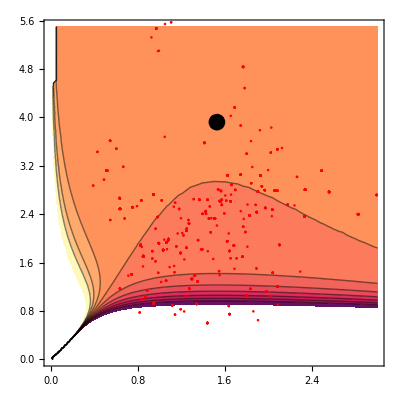

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]}
VO3=AO3 PowerExpand[(ρ^((q-6)/2)τ^-3)/.changmoduli]/.{ϕ->Log[1/s]}/.{q->3}
VF5=AF5 PowerExpand[(ρ^(3-p)τ^-4)/.changmoduli]/.{ϕ->Log[1/s]}/.{p->5}
VF5=AF5/τ^4;
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]}
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
Vins=AA Exp[-aa τ];
(*VD5=AD5/(√(s^3) τ^(3/2));*)
Vreal=VH3+VF3+0VD5+VF5+VO3+0Vins
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
max=100;
data=Table[0,{i,1,max}];
Do[
{min,steps}=Reap[
NMinimize[
{10^4 diV.diV+ 10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij),s>RandomInteger[{1,100}]/100,τ>RandomInteger[{1,100}]/100},{s,τ,AF3,AH3,AO3,AF5},
Method->{"SimulatedAnnealing","PerturbationScale"->0.5,"LevelIterations"->50,"RandomSeed"->0,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^2,WorkingPrecision->500}},
StepMonitor:>Sow[{s,τ,AF3,AH3,AO3,AA,aa}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,10]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,3},{τ,0,5.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

```mathematica
vars={s,τ,AF3,AH3,AO3,AA,aa};(*|0|*)
ListLogPlot[Table[(10^4 diV.diV+10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij))/.Thread[vars->steps⟦1⟧⟦jj⟧],{jj,1,100}]]
```

-Graphics-

87

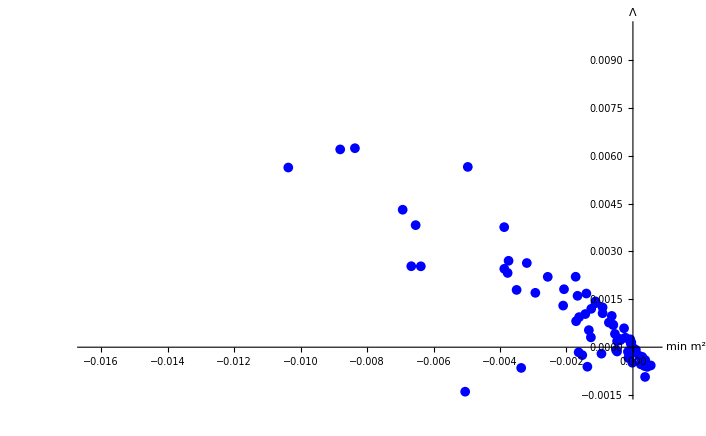

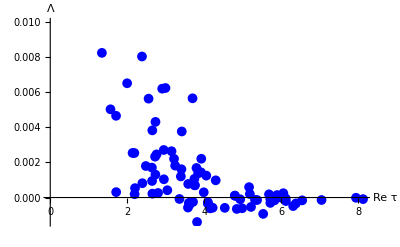
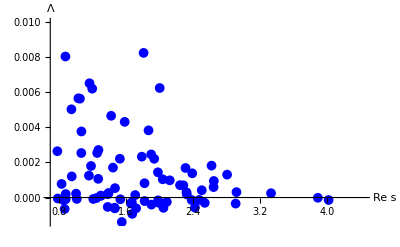

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
(*data=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];*)
$MaxExtraPrecision=10000;
max=Length[data];
datag=Table[0,{i,max}];
up=Length[data⟦1⟧]-2;
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;up⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[Re[diV/.data⟦jj⟧⟦4;;up⟧/.fr]]==0.0,
(*Print["--------------------------------------------------------------------------------------------"];*)
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;up⟧,fr,data⟦jj⟧⟦4;;up⟧,egval/.fr/.data⟦jj⟧⟦4;;up⟧}],30];
(*Print["values = ",{Vreal/.fr /.data⟦jj⟧⟦4;;8⟧,egval}/.data⟦jj⟧⟦4;;8⟧/.fr];
Print["diV = ",Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.data⟦jj⟧⟦4;;8⟧/.fr];*)
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦up+1;;up+2⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦up+1;;up+2⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1]
{ListPlot[Table[{τ21/.datag⟦i⟧⟦3⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re τ","Λ"},PlotStyle-> Blue],ListPlot[Table[{s/.datag⟦i⟧⟦2⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re s","Λ"},PlotStyle-> Blue]}
(*Save["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5",datag];*)
```

```mathematica
datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
(*datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5"];*)
```

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6.

```mathematica
Print["Stable dS"];
up=Length[datag⟦1⟧]-2;
aux1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Print["dS ",Length[aux1],". Anda the % dS is ",N@Length[aux1]/Length[datag] 100];
aux11=Table[If[ii==1,{"i","min V","m^2","m^2","s","τ","AF3","AH3","AF5","AO3","AD5"},
Flatten[{ii,aux1⟦ii⟧⟦2;;4⟧,Flatten[{s,τ,AF3,AH3,AF5,AO3,AD5,AA}/.aux1⟦ii⟧⟦5;;⟧]}]],{ii,Length[aux1]}];
Grid[N[aux11,4], Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
Print["Stable AdS"];
aux2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
aux22=Table[If[ii==1,{"min V","m^2","m^2","s","τ","AF3","AH3","AF5","AO3","AD5"},
Flatten[{aux2⟦ii⟧⟦2;;4⟧,Flatten[{s,τ,AF3,AH3,AF5,AO3,AD5,aa,AA}/.aux2⟦ii⟧⟦5;;⟧]}]],{ii,Length[aux2]}];
Print["dS ",Length[aux2],". And the % of AdS is ",N@Length[aux2]/Length[datag] 100];
Grid[aux22, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

Stable dS

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

dS 0. Anda the % dS is Indeterminate

Stable AdS

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

dS 0. And the % of AdS is Indeterminate

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

-Graphics-

{}

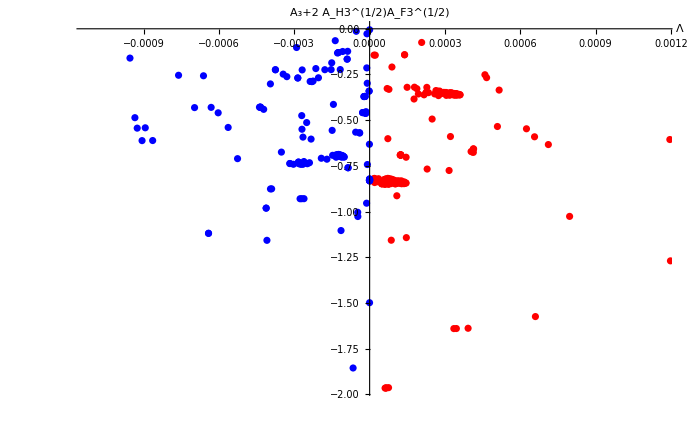

{{-0.00012464,-0.13},{-0.00039013,-0.8755},{-0.00014738,-0.6921},{-0.001391,-0.5234},{-0.00043569,-0.4291},{-0.00028337,-0.7291},{-0.000066456,-0.63967+0.10601 ⅈ},{-0.00015331,-0.2233},{-0.00042185,-0.4406},{-0.00012303,-0.6922},{-0.0002654,-0.5925},{-1.082×10^-7,-0.8223},{-0.00015092,-0.186},{-0.000018687,-0.3704},{-0.000023066,-0.3707},{-0.000040394,-0.5681},{-0.0002787,-0.42878+0.10967 ⅈ},{-0.00024805,-0.738},{-0.00012464,-0.13},{-0.00012293,-0.6884},{-0.00027035,-0.9294},{-0.00032964,-0.2619},{-0.0001369,-0.06503},{-0.000065209,-0.59035+0.11487 ⅈ},{-0.00013192,-0.6884},{-0.00026865,-0.225},{-0.000020494,-0.3704},{-0.000086673,-0.7601},{-0.00152,-0.3707},{-0.00010326,-0.7012},{-7.7393×10^-7,-0.829},{-0.00023316,-0.6033},{-0.000046925,-1.027},{-0.00011634,-0.6896},{-0.00012388,-0.6871},{-2.92×10^-8,-0.8287},{-0.00023685,-0.2881},{-0.00014418,-0.4136},{-0.0002613,-0.9292},{-0.000089468,-0.166},{-0.0001155,-0.6948},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00069702,-0.4311},{-0.00001461,-0.4534},{-0.00010828,-0.6935},{-0.00012027,-0.6959},{-0.00026936,-0.5495},{-0.00027696,-0.9296},{-0.00086381,-0.6113},{-0.001516,-0.3704},{-8.9965×10^-6,-0.7425},{-0.0009542,-0.1603},{-3.832×10^-7,-0.8288},{-0.00056327,-0.5397},{-0.00045495,-1.0037+0.14476 ⅈ},{-0.0002617,-0.7261},{-0.001487,-0.3686},{-0.000027974,-0.4585},{-0.00026535,-0.7399},{-0.00027105,-0.42869+0.10959 ⅈ},{-0.00011391,-1.104},{-0.00031757,-0.737},{-0.00020248,-1.6904+0.18222 ⅈ},{-0.00029086,-0.102},{-0.00020382,-0.2679},{-0.000089468,-0.166},{-0.00017839,-0.2238},{-0.002193,-0.8576},{-0.00022977,-0.2886},{-0.00012491,-0.6897},{-0.000053287,-0.0137},{-0.000012134,-0.9541},{-0.00019241,-0.7082},{-0.000015058,-0.4624},{-0.00012027,-0.6959},{-0.00039511,-0.3015},{-0.00013353,-0.7025},{-0.000027974,-0.4585},{-0.000016875,-0.4627},{-0.00034423,-0.248},{-0.00152,-0.3707},{-2.0643×10^-9,-0.0055},{-0.00027389,-0.7416},{-0.00008747,-0.123},{-2.264×10^-7,-0.8257},{-0.00011702,-0.223},{-0.00026535,-0.7399},{-1.1552×10^-6,-0.8281},{-0.00090608,-0.6117},{-8.1068×10^-7,-0.65609+0.16922 ⅈ},{-0.0013072,-0.3945},{-0.00022977,-0.2886},{-0.00012793,-0.1325},{-0.00063101,-0.4299},{-0.00022513,-0.286},{-0.00010573,-0.6974},{-0.00093453,-0.4862},{-0.00043411,-0.4284},{-0.000060548,-1.4939+0.42352 ⅈ},{-0.00013409,-0.6971},{-2.0834×10^-6,-0.3409},{-0.00064147,-1.119},{-2.264×10^-7,-0.8257},{-0.000047477,-1.004},{-0.000065847,-1.855},{-0.00025066,-0.513},{-5.0599×10^-6,-0.69327+0.22791 ⅈ},{-0.00037512,-0.2241},{-0.0003948,-0.8759},{-0.000085233,-0.7603},{-0.00011387,-0.7008},{-0.00041198,-0.9809},{-0.00089334,-0.5416},{-0.000017245,-0.37},{-0.0004089,-1.157},{-0.00012027,-0.6959},{-0.00076075,-0.2543},{-0.00035129,-0.6746},{-3.4703×10^-7,-0.65842+0.20357 ⅈ},{-0.00060304,-0.4596},{-0.001457,-0.3668},{-0.00028601,-0.2691},{-0.00092536,-0.5435},{-0.000022105,-0.3707},{-0.000019107,-0.37},{-0.0005259,-0.7103},{-0.00030339,-0.7411},{-0.00043569,-0.4291},{-0.0001074,-0.1242},{-0.00014924,-0.5557},{-0.00010911,-0.57674+0.14944 ⅈ},{-1.6644×10^-6,-0.65565+0.16683 ⅈ},{-6.79×10^-9,-0.8208},{-0.00010573,-0.6974},{-0.000034012,-0.5654+0.15708 ⅈ},{-0.00028337,-0.7291},{-2.0432×10^-6,-0.3408},{-3.254×10^-7,-1.498},{-0.000084681,-1.1683+0.36211 ⅈ},{-0.00021418,-0.2176},{-0.00041198,-0.9809},{-0.00043861,-0.429},{-8.247×10^-7,-0.6315},{-0.00017011,-0.7134},{-0.00011112,-0.7009},{-4.×10^-10,-0.8317},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00064147,-1.119},{-0.000011399,-0.214},{-0.00023955,-0.7326},{-0.00028207,-0.738},{-0.000039472,-0.5703},{-0.0039455,-0.4976},{-0.000010682,-0.0276},{-0.00012935,-0.6954},{-0.000018787,-0.4596},{-0.00066149,-0.257},{-0.00028731,-0.42886+0.10966 ⅈ},{-0.00028261,-0.42883+0.10971 ⅈ},{-0.00037512,-0.2241},{-9.5848×10^-6,-0.2981},{-0.00031757,-0.737},{-0.00010573,-0.6974},{-0.00027033,-0.4749},{-0.000055618,-0.5655},{-0.00028601,-0.2691},{-0.0015105,-0.3701},{-4.×10^-10,-0.8317},{-0.00010929,-0.6998},{-0.00010075,-0.7012}}

-Graphics-

{{-0.00012464,-0.13},{-0.00039013,-0.8755},{-0.00014738,-0.6921},{-0.001391,-0.5234},{-0.00043569,-0.4291},{-0.00028337,-0.7291},{-0.000066456,-0.63967+0.10601 ⅈ},{-0.00015331,-0.2233},{-0.00042185,-0.4406},{-0.00012303,-0.6922},{-0.0002654,-0.5925},{-1.082×10^-7,-0.8223},{-0.00015092,-0.186},{-0.000018687,-0.3704},{-0.000023066,-0.3707},{-0.000040394,-0.5681},{-0.0002787,-0.42878+0.10967 ⅈ},{-0.00024805,-0.738},{-0.00012464,-0.13},{-0.00012293,-0.6884},{-0.00027035,-0.9294},{-0.00032964,-0.2619},{-0.0001369,-0.06503},{-0.000065209,-0.59035+0.11487 ⅈ},{-0.00013192,-0.6884},{-0.00026865,-0.225},{-0.000020494,-0.3704},{-0.000086673,-0.7601},{-0.00152,-0.3707},{-0.00010326,-0.7012},{-7.7393×10^-7,-0.829},{-0.00023316,-0.6033},{-0.000046925,-1.027},{-0.00011634,-0.6896},{-0.00012388,-0.6871},{-2.92×10^-8,-0.8287},{-0.00023685,-0.2881},{-0.00014418,-0.4136},{-0.0002613,-0.9292},{-0.000089468,-0.166},{-0.0001155,-0.6948},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00069702,-0.4311},{-0.00001461,-0.4534},{-0.00010828,-0.6935},{-0.00012027,-0.6959},{-0.00026936,-0.5495},{-0.00027696,-0.9296},{-0.00086381,-0.6113},{-0.001516,-0.3704},{-8.9965×10^-6,-0.7425},{-0.0009542,-0.1603},{-3.832×10^-7,-0.8288},{-0.00056327,-0.5397},{-0.00045495,-1.0037+0.14476 ⅈ},{-0.0002617,-0.7261},{-0.001487,-0.3686},{-0.000027974,-0.4585},{-0.00026535,-0.7399},{-0.00027105,-0.42869+0.10959 ⅈ},{-0.00011391,-1.104},{-0.00031757,-0.737},{-0.00020248,-1.6904+0.18222 ⅈ},{-0.00029086,-0.102},{-0.00020382,-0.2679},{-0.000089468,-0.166},{-0.00017839,-0.2238},{-0.002193,-0.8576},{-0.00022977,-0.2886},{-0.00012491,-0.6897},{-0.000053287,-0.0137},{-0.000012134,-0.9541},{-0.00019241,-0.7082},{-0.000015058,-0.4624},{-0.00012027,-0.6959},{-0.00039511,-0.3015},{-0.00013353,-0.7025},{-0.000027974,-0.4585},{-0.000016875,-0.4627},{-0.00034423,-0.248},{-0.00152,-0.3707},{-2.0643×10^-9,-0.0055},{-0.00027389,-0.7416},{-0.00008747,-0.123},{-2.264×10^-7,-0.8257},{-0.00011702,-0.223},{-0.00026535,-0.7399},{-1.1552×10^-6,-0.8281},{-0.00090608,-0.6117},{-8.1068×10^-7,-0.65609+0.16922 ⅈ},{-0.0013072,-0.3945},{-0.00022977,-0.2886},{-0.00012793,-0.1325},{-0.00063101,-0.4299},{-0.00022513,-0.286},{-0.00010573,-0.6974},{-0.00093453,-0.4862},{-0.00043411,-0.4284},{-0.000060548,-1.4939+0.42352 ⅈ},{-0.00013409,-0.6971},{-2.0834×10^-6,-0.3409},{-0.00064147,-1.119},{-2.264×10^-7,-0.8257},{-0.000047477,-1.004},{-0.000065847,-1.855},{-0.00025066,-0.513},{-5.0599×10^-6,-0.69327+0.22791 ⅈ},{-0.00037512,-0.2241},{-0.0003948,-0.8759},{-0.000085233,-0.7603},{-0.00011387,-0.7008},{-0.00041198,-0.9809},{-0.00089334,-0.5416},{-0.000017245,-0.37},{-0.0004089,-1.157},{-0.00012027,-0.6959},{-0.00076075,-0.2543},{-0.00035129,-0.6746},{-3.4703×10^-7,-0.65842+0.20357 ⅈ},{-0.00060304,-0.4596},{-0.001457,-0.3668},{-0.00028601,-0.2691},{-0.00092536,-0.5435},{-0.000022105,-0.3707},{-0.000019107,-0.37},{-0.0005259,-0.7103},{-0.00030339,-0.7411},{-0.00043569,-0.4291},{-0.0001074,-0.1242},{-0.00014924,-0.5557},{-0.00010911,-0.57674+0.14944 ⅈ},{-1.6644×10^-6,-0.65565+0.16683 ⅈ},{-6.79×10^-9,-0.8208},{-0.00010573,-0.6974},{-0.000034012,-0.5654+0.15708 ⅈ},{-0.00028337,-0.7291},{-2.0432×10^-6,-0.3408},{-3.254×10^-7,-1.498},{-0.000084681,-1.1683+0.36211 ⅈ},{-0.00021418,-0.2176},{-0.00041198,-0.9809},{-0.00043861,-0.429},{-8.247×10^-7,-0.6315},{-0.00017011,-0.7134},{-0.00011112,-0.7009},{-4.×10^-10,-0.8317},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00064147,-1.119},{-0.000011399,-0.214},{-0.00023955,-0.7326},{-0.00028207,-0.738},{-0.000039472,-0.5703},{-0.0039455,-0.4976},{-0.000010682,-0.0276},{-0.00012935,-0.6954},{-0.000018787,-0.4596},{-0.00066149,-0.257},{-0.00028731,-0.42886+0.10966 ⅈ},{-0.00028261,-0.42883+0.10971 ⅈ},{-0.00037512,-0.2241},{-9.5848×10^-6,-0.2981},{-0.00031757,-0.737},{-0.00010573,-0.6974},{-0.00027033,-0.4749},{-0.000055618,-0.5655},{-0.00028601,-0.2691},{-0.0015105,-0.3701},{-4.×10^-10,-0.8317},{-0.00010929,-0.6998},{-0.00010075,-0.7012}}

-Graphics-

```mathematica
up=Length[datag⟦1⟧]-2;
datag1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
datag2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{datag1⟦jj⟧⟦1⟧,(AO3+2 AH3^(1/2)AF3^(1/2))/.datag1⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag1]}];
l2=Table[{datag2⟦jj⟧⟦1⟧,(AO3+2 AH3^(1/2)AF3^(1/2))/.datag2⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag2]}];
l2
f1=ListPlot[{l1,l2},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20},AxesLabel->{"Λ","A_3+2 A_H3^(1/2)A_F3^(1/2)"},ImageSize->700]
```

```mathematica
inter=aux1⟦6⟧⟦1⟧;
Print["values = ",datag⟦inter⟧];
Vold=Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧;
eqs=Table[D[Vold,var⟦i⟧],{i,1,2}];
sol=Quiet@Solve[Thread[%==0],var]⟦2⟧;
Print["AdS: Exact solution: ",{(AF3/AH3)^(1/2),(-4/3)AF5/(AO3+2 AH3^(1/2)AF3^(1/2))}/.datag⟦inter⟧⟦4;;up⟧,"vs numerical sol: ",sol];
(*******************************************)
poly=(Expand[-2 AF3^3+3 AF3^2 AO3 s+(AD5^2 AF5+12 AF3^2 AH3) s^2-6 AF3 AH3 AO3 s^3-18 AF3 AH3^2 s^4+3 AH3^2 AO3 s^5+8 AH3^3 s^6]);
auxsols=N[NSolve[(poly/.Rationalize[datag⟦inter⟧⟦4;;8⟧,10^-100])==0,s,WorkingPrecision->10]⟦5⟧,30];
Print["dS: Exact solution: ",{s/.auxsols,(4(-AF3+AH3 s^2)^2)/(AD5^2 s)/.Rationalize[datag⟦inter⟧⟦4;;8⟧,10^-100]/.auxsols}," vs numerical sol: ",datag⟦inter⟧⟦2;;3⟧];
(*******************************************)
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧," -> ",diV/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol]
Print[sol,"->",datag⟦inter⟧⟦2;;3⟧];
Print[Eigenvalues[mij/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol],"->",datag⟦inter⟧⟦up+1;;up+2⟧];
Print["V = ",Vold/.sol,"-> V = ",datag⟦inter⟧⟦1⟧];
{fo=Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"},PlotStyle->Blue,ImageSize->{300}],
foτ=Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]2.1},PlotStyle->Blue,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{300}]}
{fn=Plot[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦2⟧,{s,Evaluate[(s/.sol⟦1⟧)] 0.9,Evaluate[(s/.sol⟦1⟧)]1.1},PlotStyle->Red,ImageSize->{300},BaseStyle->{FontSize->20,FontFamily->"Times"}],
Plot[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦1⟧,{τ,Evaluate[(τ/.sol⟦2⟧)] 0.9,Evaluate[(τ/.sol⟦2⟧)]1.1},PlotStyle->Red,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{300}]}
```

Part::partw: Part 6 of {} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

values = Symbol[]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 4 through 0 in Symbol[].

ReplaceAll::reps: {Symbol[]⟦4;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 4 through 0 in Symbol[].

ReplaceAll::reps: {Symbol[]⟦4;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AdS: Exact solution: {√(AF3/AH3),-(4 AF5)/(3 (2 √AF3 √AH3+AO3))}/.Symbol[]⟦4;;0⟧vs numerical sol: {{}}⟦2⟧

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 4 through 8 in Symbol[].

ReplaceAll::reps: {Symbol[]⟦4;;8⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 4 through 8 in Symbol[].

ReplaceAll::reps: {Symbol[]⟦4;;8⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 2 through 3 in Symbol[].

dS: Exact solution: {Root[-2. AF3^3+3. AF3^2 AO3 #1+(AD5^2 AF5+12. AF3^2 AH3) #1^2-6. AF3 AH3 AO3 #1^3-18. AF3 AH3^2 #1^4+3. AH3^2 AO3 #1^5+8. AH3^3 #1^6-1. InverseFunction[ReplaceAll,1,2][0,Symbol[]⟦4;;8⟧]&,5],(4 (-AF3+AH3 Root[-2. AF3^3+3. AF3^2 AO3 #1+(AD5^2 AF5+12. AF3^2 AH3) #1^2-6. AF3 AH3 AO3 #1^3-18. AF3 AH3^2 #1^4+3. AH3^2 AO3 #1^5+8. AH3^3 #1^6-1. InverseFunction[ReplaceAll,1,2][0,Symbol[]⟦4;;8⟧]&,5]^2)^2)/(AD5^2 Root[-2. AF3^3+3. AF3^2 AO3 #1+(AD5^2 AF5+12. AF3^2 AH3) #1^2-6. AF3 AH3 AO3 #1^3-18. AF3 AH3^2 #1^4+3. AH3^2 AO3 #1^5+8. AH3^3 #1^6-1. InverseFunction[ReplaceAll,1,2][0,Symbol[]⟦4;;8⟧]&,5])/.Symbol[]⟦4;;8⟧} vs numerical sol: Symbol[]⟦2;;3⟧

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 2 through 0 in Symbol[].

ReplaceAll::reps: {Symbol[]⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 4 through 0 in Symbol[].

ReplaceAll::reps: {Symbol[]⟦4;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

diV = {(AH3-AF3/s^2)/τ^3,(-4 AF5 s-3 (AF3+s (AO3+AH3 s)) τ)/(s τ^5)}/.Symbol[]⟦2;;0⟧ -> {(AH3-AF3/s^2)/τ^3,(-4 AF5 s-3 (AF3+s (AO3+AH3 s)) τ)/(s τ^5)}/.Symbol[]⟦4;;0⟧/.{{}}⟦2⟧

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 2 through 3 in Symbol[].

{{}}⟦2⟧->Symbol[]⟦2;;3⟧

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 4 through 0 in Symbol[].

ReplaceAll::reps: {Symbol[]⟦4;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 2 in Symbol[].

Eigenvalues[{{(2 AF3)/(s^3 τ^3),(3 (AF3-AH3 s^2))/(s^2 τ^4)},{(3 (AF3-AH3 s^2))/(s^2 τ^4),(4 (5 AF5 s+3 (AF3+s (AO3+AH3 s)) τ))/(s τ^6)}}/.Symbol[]⟦4;;0⟧/.{{}}⟦2⟧]->Symbol[]⟦1;;2⟧

ReplaceAll::reps: {{{}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of Symbol[] does not exist.

V = AF5/τ^4+AO3/τ^3+AF3/(s τ^3)+(AH3 s)/τ^3/.Symbol[]⟦4;;0⟧/.{{}}⟦2⟧-> V = Symbol[]⟦1⟧

ReplaceAll::reps: {Symbol[]⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::take: Cannot take positions 2 through 0 in Symbol[].

ReplaceAll::reps: {Symbol[]⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ReplaceAll::reps: {Symbol[]⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 2 through 0 in Symbol[].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Part::take will be suppressed during this calculation.

Plot::plln: Limiting value 0.9 (s/.Symbol[]⟦2;;0⟧) in {s,0.9 (s/.Symbol[]⟦2;;0⟧),1.1 (s/.Symbol[]⟦2;;0⟧)} is not a machine-sized real number.

Plot::plln: Limiting value 0.9 (τ/.Symbol[]⟦2;;0⟧) in {τ,0.9 (τ/.Symbol[]⟦2;;0⟧),2.1 (τ/.Symbol[]⟦2;;0⟧)} is not a machine-sized real number.

{Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[s/.datag⟦inter⟧⟦2;;up⟧] 0.9,Evaluate[s/.datag⟦inter⟧⟦2;;up⟧] 1.1},AxesLabel→{s,V},PlotStyle→Blue,ImageSize→{300}],Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[τ/.datag⟦inter⟧⟦2;;up⟧] 0.9,Evaluate[τ/.datag⟦inter⟧⟦2;;up⟧] 2.1},PlotStyle→Blue,BaseStyle→{FontSize→20,FontFamily→Times},ImageSize→{300}]}

Plot::plln: Limiting value {0.9 s} in {s,{0.9 s},{1.1 s}} is not a machine-sized real number.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {2.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Plot::plln: Limiting value 0.9 (τ/.2) in {τ,0.9 (τ/.2),1.1 (τ/.2)} is not a machine-sized real number.

{Plot[Vreal/.{AD5→0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦2⟧,{s,Evaluate[s/.sol⟦1⟧] 0.9,Evaluate[s/.sol⟦1⟧] 1.1},PlotStyle→Red,ImageSize→{300},BaseStyle→{FontSize→20,FontFamily→Times}],Plot[Vreal/.{AD5→0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦1⟧,{τ,Evaluate[τ/.sol⟦2⟧] 0.9,Evaluate[τ/.sol⟦2⟧] 1.1},PlotStyle→Red,BaseStyle→{FontSize→20,FontFamily→Times},ImageSize→{300}]}

```mathematica
Plot[{Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦2⟧,Vreal/.datag⟦inter⟧⟦3;;up⟧},{s,Evaluate[(s/.sol⟦1⟧)] 0.5,Evaluate[(s/.sol⟦1⟧)]2.5},PlotRange->{-0.062,0.005},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{700}]
Plot[{Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦1⟧,Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧},{τ,Evaluate[(τ/.sol⟦2⟧)] 0.5,Evaluate[(τ/.sol⟦2⟧)]5.5},PlotRange->{-0.062,0.0062},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20,FontFamily->"Times"},Epilog->Inset[foτ,{6,-0.04}],ImageSize->{700}]
```

Plot::plln: Limiting value {0.5 s} in {s,{0.5 s},{2.5 s}} is not a machine-sized real number.

Plot[{Vreal/.{AD5→0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦2⟧,Vreal/.datag⟦inter⟧⟦3;;up⟧},{s,Evaluate[s/.sol⟦1⟧] 0.5,Evaluate[s/.sol⟦1⟧] 2.5},PlotRange→{-0.062,0.005},PlotStyle→{Red,Blue},BaseStyle→{FontSize→20,FontFamily→Times},ImageSize→{700}]

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {2.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Plot::plln: Limiting value 0.5 (τ/.2) in {τ,0.5 (τ/.2),5.5 (τ/.2)} is not a machine-sized real number.

Plot[{Vreal/.{AD5→0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦1⟧,Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧},{τ,Evaluate[τ/.sol⟦2⟧] 0.5,Evaluate[τ/.sol⟦2⟧] 5.5},PlotRange→{-0.062,0.0062},PlotStyle→{Red,Blue},BaseStyle→{FontSize→20,FontFamily→Times},Epilog→Inset[foτ,{6,-0.04}],ImageSize→{700}]

```mathematica
(*Plot[{Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧},{τ,Evaluate[(τ/.sol⟦2⟧)] 0.95,Evaluate[(τ/.sol⟦2⟧)]25.5},AxesLabel->{"τ","V"},PlotRange->{-0.001,0.0062},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{700}]*)
Veff=Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧;
ϕfv1=τ/.datag⟦inter⟧⟦2;;3⟧⟦2⟧
edo[ϕfv_,Vreal1_]:={s D[τp[s],s,s]+3 D[τp[s],s]==s(D[Vreal1,τ]/.τ->τp[s]),τp[10^2]==ϕfv,τp'[1/1000]==0.0};
NDSolve[edo[ϕfv1,Veff],τp[s],{s,1,1000}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of Symbol[] does not exist.

ReplaceAll::reps: {Symbol[]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 4 through 0 in Symbol[].

ReplaceAll::reps: {Symbol[]⟦4;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 2 through 3 in Symbol[].

ReplaceAll::reps: {2;;3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

τ/.2;;3

ReplaceAll::reps: {Symbol[]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Symbol[]⟦4;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Power::infy: Infinite expression 1/0.^4 encountered.

Power::infy: Infinite expression 1/0.^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

ReplaceAll::reps: {Symbol[]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

D::ivar: 0. is not a valid variable.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

D::ivar: 0. is not a valid variable.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

NDSolve::ndnum: Encountered non-numerical value for a derivative at s == 0.001.

NDSolve[{3 τp'[s]+s τp''[s]==s ∂_τp[s] (AF5/τp[s]^4+AO3/τp[s]^3+AF3/(s τp[s]^3)+(AH3 s)/τp[s]^3/.Symbol[]⟦2⟧/.Symbol[]⟦4;;0⟧),τp[100]==(τ/.2;;3),τp'[1/1000]==0.},τp[s],{s,1,1000}]

```mathematica
inter=1616;
Print["values = ",datag⟦inter⟧];
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧]
Vold=Rationalize[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧,10^-1000];
eqs=Table[D[Vold,var⟦i⟧],{i,1,2}];
sol=N@Solve[Thread[%==0],var]⟦2⟧
Print[Eigenvalues[mij/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol],"->",datag⟦inter⟧⟦up+1;;up+2⟧];
Print["V = ",datag⟦inter⟧⟦1⟧,"-> V = ",Vold/.sol];
{Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"}],
Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"τ","V"}]}
Plot3D[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1}]
```

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

values = $Failed⟦1616⟧

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

Part::take: Cannot take positions 2 through 0 in $Failed⟦1616⟧.

ReplaceAll::reps: {$Failed⟦1616⟧⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

diV = {(AH3-AF3/s^2)/τ^3,(-4 AF5 s-3 (AF3+s (AO3+AH3 s)) τ)/(s τ^5)}/.$Failed⟦1616⟧⟦2;;0⟧

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

Part::take: Cannot take positions 4 through 0 in $Failed⟦1616⟧.

ReplaceAll::reps: {$Failed⟦1616⟧⟦4;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{}} does not exist.

{{}}⟦2⟧

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

Part::take: Cannot take positions 4 through 0 in $Failed⟦1616⟧.

ReplaceAll::reps: {$Failed⟦1616⟧⟦4;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

Eigenvalues[{{(2 AF3)/(s^3 τ^3),(3 (AF3-AH3 s^2))/(s^2 τ^4)},{(3 (AF3-AH3 s^2))/(s^2 τ^4),(4 (5 AF5 s+3 (AF3+s (AO3+AH3 s)) τ))/(s τ^6)}}/.$Failed⟦1616⟧⟦4;;0⟧/.{{}}⟦2⟧]->$Failed⟦1616⟧

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

ReplaceAll::reps: {{{}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

V = $Failed-> V = AF5/τ^4+AO3/τ^3+AF3/(s τ^3)+(AH3 s)/τ^3/.$Failed⟦1616⟧⟦4;;0⟧/.{{}}⟦2⟧

ReplaceAll::reps: {$Failed⟦1616⟧⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::take: Cannot take positions 2 through 0 in $Failed⟦1616⟧.

ReplaceAll::reps: {$Failed⟦1616⟧⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

ReplaceAll::reps: {$Failed⟦1616⟧⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

Part::take: Cannot take positions 2 through 0 in $Failed⟦1616⟧.

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

General::stop: Further output of Part::take will be suppressed during this calculation.

Plot::plln: Limiting value 0.9 (s/.$Failed⟦1616⟧⟦2;;0⟧) in {s,0.9 (s/.$Failed⟦1616⟧⟦2;;0⟧),1.1 (s/.$Failed⟦1616⟧⟦2;;0⟧)} is not a machine-sized real number.

Plot::plln: Limiting value 0.9 (τ/.$Failed⟦1616⟧⟦2;;0⟧) in {τ,0.9 (τ/.$Failed⟦1616⟧⟦2;;0⟧),1.1 (τ/.$Failed⟦1616⟧⟦2;;0⟧)} is not a machine-sized real number.

{Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[s/.datag⟦inter⟧⟦2;;up⟧] 0.9,Evaluate[s/.datag⟦inter⟧⟦2;;up⟧] 1.1},AxesLabel→{s,V}],Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[τ/.datag⟦inter⟧⟦2;;up⟧] 0.9,Evaluate[τ/.datag⟦inter⟧⟦2;;up⟧] 1.1},AxesLabel→{τ,V}]}

ReplaceAll::reps: {$Failed⟦1616⟧⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::take: Cannot take positions 2 through 0 in $Failed⟦1616⟧.

ReplaceAll::reps: {$Failed⟦1616⟧⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

ReplaceAll::reps: {$Failed⟦1616⟧⟦2;;0⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

Part::take: Cannot take positions 2 through 0 in $Failed⟦1616⟧.

Part::partd: Part specification $Failed⟦1616⟧ is longer than depth of object.

General::stop: Further output of Part::take will be suppressed during this calculation.

Plot3D::plln: Limiting value 0.9 (s/.$Failed⟦1616⟧⟦2;;0⟧) in {s,0.9 (s/.$Failed⟦1616⟧⟦2;;0⟧),1.1 (s/.$Failed⟦1616⟧⟦2;;0⟧)} is not a machine-sized real number.

Plot3D[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[s/.datag⟦inter⟧⟦2;;up⟧] 0.9,Evaluate[s/.datag⟦inter⟧⟦2;;up⟧] 1.1},{τ,Evaluate[τ/.datag⟦inter⟧⟦2;;up⟧] 0.9,Evaluate[τ/.datag⟦inter⟧⟦2;;up⟧] 1.1}]

```mathematica
(*Save["C:\\Users\\Cesar\\Dropbox\\Source-codes\\penalty-cases-AdS-noT",data]*)
```

```mathematica
caseso3gp⟦1⟧
```

Part::partd: Part specification caseso3gp⟦1⟧ is longer than depth of object.

caseso3gp⟦1⟧

```mathematica
caseso3=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g"];
f1=ListPlot[Table[{Min[caseso3⟦i⟧⟦9;;10⟧],caseso3⟦i⟧⟦1⟧},{i,Length[caseso3]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o7g"];
f2=ListPlot[Table[{Min[caseso3g⟦i⟧⟦9;;10⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g"];
f3=ListPlot[Table[{Min[caseso3g⟦i⟧⟦8;;9⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Green,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g-pos"];
f4=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦8;;9⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];
f5=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦10;;11⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3F5=Get["/Users/cesar/Dropbox/Source-codes/penalty-F5-o3g-noD5-2"];
f6=ListPlot[Table[{Min[caseso3F5⟦i⟧⟦8;;9⟧],caseso3F5⟦i⟧⟦1⟧},{i,Length[caseso3F5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];
casenoAR=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
f7=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
casenoARnp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty"];
f8=ListPlot[Table[{Min[casenoARnp⟦i⟧⟦9;;10⟧],casenoARnp⟦i⟧⟦1⟧},{i,Length[casenoARnp]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
(*caseoscar=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-oscarproposal"];
f9=ListPlot[Table[{Min[caseoscar⟦i⟧⟦9;;10⟧],caseoscar⟦i⟧⟦1⟧},{i,Length[caseoscar]}],BaseStyle->{FontSize->20},PlotMarkers->{"\[KernelIcon]",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];*)

(*Show[f5,f6,f1,f3,f2]*)
Show[f7,f10]
casenoARnod5⟦1⟧
casenoAR⟦1⟧
(*penalty-random-o3g-noAR6*)
```

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o7g.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o5g.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o5g-pos.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-F5-o3g-noD5-2.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty.

Show::gcomb: Could not combine the graphics objects in Show[,f10].

Show[-Graphics-,f10]

Part::partd: Part specification casenoARnod5⟦1⟧ is longer than depth of object.

casenoARnod5⟦1⟧

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

$Failed⟦1⟧

```mathematica
casenoARnod5=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5"];
f10z=ListPlot[Table[{Min[casenoARnod5⟦i⟧⟦8;;9⟧],casenoARnod5⟦i⟧⟦1⟧},{i,Length[casenoARnod5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","|Λ|"},PlotStyle-> Black,ImageSize->700,PlotRange->{{0.0,0.002},{0.0,-0.002}}];
f10=ListPlot[Table[{Min[casenoARnod5⟦i⟧⟦8;;9⟧],casenoARnod5⟦i⟧⟦1⟧},{i,Length[casenoARnod5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];
casenoAR=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
f7z=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700,PlotRange->{{0.0,0.002},{-0.002,0.002}}];
f7=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
Show[f7z,f10z]
(*Show[f5,f6,f1,f3,f2]*)
```

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6.

-Graphics-

### Machine learning

```mathematica
(*datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];*)
up=Length[datag⟦1⟧]-2;
varsNN={AF3,AH3,AD5,AO3,AF5};
dataNNv=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->Chop[datag⟦jj⟧⟦1⟧],{jj,1,Length[datag]}]
frac=0.3;
{nvs2tes,nvs2tra}=TakeDrop[dataNNv,Round[frac*Length[dataNNv]]];
net=NetChain[{32,Tanh,1},"Input"-> {5},"Output"->"Scalar"];
(*net=NetInitialize[net]*)
trainedv=NetTrain[net,nvs2tra,ValidationSet->nvs2tes,TargetDevice->"CPU"]
(*net=NetChain[{45,Tanh,1},"Input"->6,"Output"->"Scalar"];
traineds=NetTrain[net,dataNNs,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->"Scalar"];
trainedτ=NetTrain[net,dataNNτ,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->1]
net1=NetTrain[net,dataNN,BatchSize->1024]*)
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

{}

NetDecoder::deprec: "NetDecoder[{Scalar,…}]" setting has been deprecated. Use ""Real" or "Integer" bare port specifications" setting instead.

NetTrain::nodata: No training data provided.

$Failed

```mathematica
2
```

2

```mathematica
trainedv
```

$Failed

```mathematica
data=Flatten@Table[{x,y}->Exp[-Norm[{x,y}]],{x,-3,3,.005},{y,-3,3,.005}];
net=NetChain[{32,Tanh,2}];
trained=NetTrain[net,data,BatchSize->1024]
```

NetTrain::invindim3: Data provided to port "Output" should be a non-empty list of length-2 vectors of real numbers, but was a length-1442401 vector of real numbers.

$Failed

```mathematica
NetMeasurements[trained,nvs2cv,"Accuracy"]
```

NetMeasurements::invnet: First argument to NetMeasurements should be a fully specified net.

$Failed

```mathematica
datag1=DeleteCases[Table[If[Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{AO3/.datag1⟦jj⟧⟦2;;up⟧,datag1⟦jj⟧⟦1⟧},{jj,1,Length[datag1]}];
ListPlot[FindClusters[l1,3,Method->"KMeans"]]
```

FindClusters::mlmpty: The dataset should contain at least one informative example (non-missing) for training.

FindClusters::numclus: The number of clusters 3. can only be either a positive integer or Automatic.

General::stop: Further output of FindClusters::numclus will be suppressed during this calculation.

FindClusters::nonopt: Options expected (instead of 2) beyond position 2 in FindClusters[0,0,2]. An option must be a rule or a list of rules.

FindClusters::nonopt: Options expected (instead of False) beyond position 2 in FindClusters[True,False,False]. An option must be a rule or a list of rules.

ListPlot::lpn: FindClusters[{},3.,Method→KMeans] is not a list of numbers or pairs of numbers.

ListPlot[FindClusters[{},3,Method→KMeans]]

## Calibration

```mathematica
var={x,y};
NM=Length[var];

mij=Simplify[Table[D[f[x,y],var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
diV=Simplify[Table[D[f[x,y],var⟦i⟧],{i,1,NM}]];
Solve[Table[D[f[x,y],var⟦i⟧]==0,{i,1,2}],var]
Plot3D[f[x,y],{x,-6,6},{y,-6,6}]
pfun=α1 If[#1<0,#1^2,0]+α2 If[#2<0,#2^2,0] &;
NMinimize[f[x,y],{x,y},Method->{"SimulatedAnnealing","PenaltyFunction"->pfun}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[{f^(1,0)[x,y]==0,f^(0,1)[x,y]==0},{x,y}]

-Graphics3D-

NMinimize::nnum: The function value f[0.9186212148724065128572064853020638361093,0.7166887533790196052052579034352675080299] is not a number at {x,y} = {0.9186212148724065128572064853020638361093,0.7166887533790196052052579034352675080299}.

NMinimize[f[x,y],{x,y},Method→{SimulatedAnnealing,PenaltyFunction→(α1 If[#1<0,#1^2,0]+α2 If[#2<0,#2^2,0]&)}]

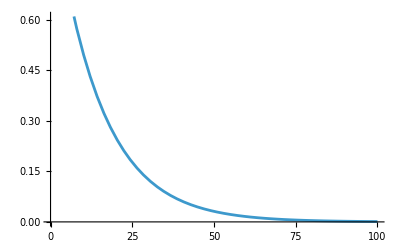

```mathematica
Plot[Exp[-(deltaF Log[1+1])/10],{deltaF,0,100}]
```

NMinimize::precw: The precision of the argument function (20+ⅇ-20 ⅇ^(-0.141421 √(x^2+y^2))-ⅇ^(0.5 (Cos[2 π x]+Cos[2 π y]))) is less than WorkingPrecision (40).

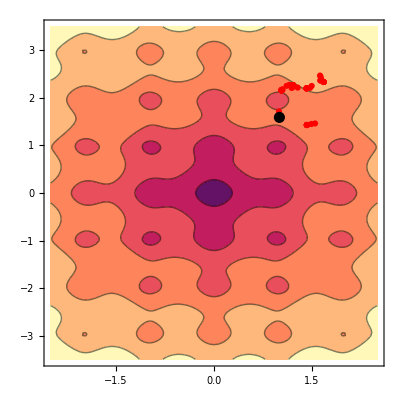

{x→1.,y→1.59076818393784966716422757881053871195}

```mathematica
f[x_,y_]:=(x+2y-7)^2+(2x+y-5)^2;
f[x_,y_]:=-20 Exp[-0.2 √(0.5(x^2+y^2))]-Exp[0.5 (Cos[2π x]+Cos[2 π y])]+Exp[1]+20;
{min,steps}=Reap[
NMinimize[
{f[x,y],x>1,y>1},{x,y},
Method->{"SimulatedAnnealing","PerturbationScale"->.1,"PenaltyFunction"->Function[{x,y},Exp[x+y]]},
StepMonitor:>Sow[{x,y}]]];
Show[ContourPlot[f[x,y],{x,-2.5,2.5},{y,-3.5,3.5},Epilog->{PointSize[0.02],Point[{x,y}/.min⟦2⟧]}],ListPlot[steps,PlotStyle->Red]]
min⟦2⟧
```

## Intento 2

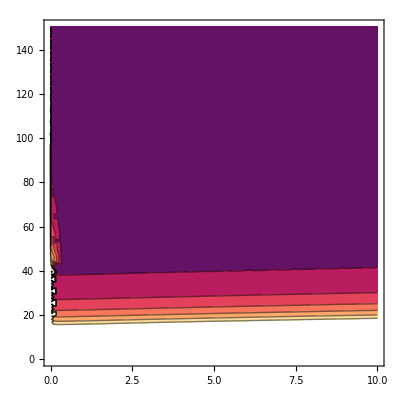

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
Vreal=VH3+VF3+VR6+VD5;
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},If[egval⟦1⟧<0,1000,0]+If[egval⟦2⟧<0,1000,0]+100/(s+1)+100/(τ+1)+ If[Vreal<0,1000,0]];
SetOptions[NMinimize,AccuracyGoal-> 0.001,MaxIterations->500,WorkingPrecision->40];
max=5;
data=Table[0,{i,1,max}];
Do[
invalue=Table[{RandomReal[{20,200}],RandomReal[{20,200}],RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}]},{ii,1,50}];
{min,steps}=Reap[
NMinimize[{(diV⟦1⟧^2+diV⟦2⟧^2)+10(Abs[egval⟦1⟧]-egval⟦1⟧)+10 (Abs[egval⟦1⟧]-egval⟦1⟧)+100/(s+1)+100/(τ+1)+ 10(Abs[Vreal]-Vreal),s>5,τ>taur},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->2.5,"LevelIterations"->200,"SearchPoints"->Automatic,"InitialPoints"->invalue,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^-3,WorkingPrecision->10^3}},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,400]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,10},{τ,0,150.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

```mathematica
Do[
ndiV=diV/.data⟦kk⟧⟦4;;7⟧;
Print["data = ",data⟦kk⟧];
Print["sol = ",NSolve[Table[ndiV⟦ii⟧==0,{ii,1,2}],{s,τ}]],{kk,1,5}]
```

data = {0.008478237638,s→25029.99578,τ→22304.54174,AF3→-7.061676677,AH3→396.4830085,AD5→14.37188713,AR6→387.5674636,-7.286662264×10^-16,3.169678717×10^-14}

sol = {{s→0.119132303 ⅈ,τ→-0.334547733 ⅈ},{s→-0.119132303 ⅈ,τ→0.334547733 ⅈ}}

data = {0.009011160709,s→19445.64992,τ→25846.22803,AF3→-5.062234156,AH3→297.671762,AD5→7.86955581,AR6→332.106184,-3.68857489×10^-16,1.08562555×10^-14}

sol = {{s→0.12031352 ⅈ,τ→-0.304662783 ⅈ},{s→-0.12031352 ⅈ,τ→0.304662783 ⅈ}}

data = {0.1033907936,s→1795.139929,τ→2094.739938,AF3→9.316395231,AH3→1.477838196,AD5→-0.6729842119,AR6→12.56510916,-1.126351422×10^-14,4.716002999×10^-12}

sol = {{s→-2.50927231-0.067622531 ⅈ,τ→0.885237091+0.039770778 ⅈ},{s→-2.50927231+0.067622531 ⅈ,τ→0.885237091-0.039770778 ⅈ},{s→2.50927231-0.067622531 ⅈ,τ→-0.885237091+0.039770778 ⅈ},{s→2.50927231+0.067622531 ⅈ,τ→-0.885237091-0.039770778 ⅈ}}

data = {0.09083925489,s→2155.814189,τ→2247.475687,AF3→-1.263379643,AH3→9.417367928,AD5→0.4576995126,AR6→8.663020071,-1.893479526×10^-13,6.475270376×10^-12}

sol = {{s→0.345417576 ⅈ,τ→-1.07977986 ⅈ},{s→-0.345417576 ⅈ,τ→1.07977986 ⅈ}}

data = {0.01059721079,s→15414.83043,τ→24327.69562,AF3→7.133891319,AH3→234.0336919,AD5→11.09150436,AR6→285.4416495,-3.879006959×10^-16,1.035776947×10^-14}

sol = {}

```mathematica
RandomReal[{20,200},{50,6}]
```

{{45.433,71.3261,81.0424,83.5776,119.27,157.896},{37.5675,134.9,40.3095,59.8036,132.301,146.61},{74.1571,155.853,82.1529,96.2901,120.505,196.582},{154.576,129.058,37.5372,101.08,188.178,133.184},{129.476,37.4738,146.706,158.628,99.2878,77.4923},{151.874,22.0677,151.956,195.496,59.6138,32.6359},{50.8022,150.93,120.256,156.83,161.456,157.891},{69.8286,134.321,131.51,191.094,32.8696,28.2219},{56.5813,167.611,33.4004,154.699,172.43,151.129},{86.6864,183.186,145.879,188.104,34.4852,101.733},{75.4755,84.3563,189.244,192.509,66.6291,20.1739},{145.61,135.985,45.5411,56.2848,188.391,42.1019},{40.963,179.928,151.433,57.4893,146.18,137.95},{34.5133,183.428,164.676,122.229,86.568,148.285},{83.0174,48.3385,175.77,70.5857,164.588,144.272},{190.114,52.7277,139.649,91.3583,114.469,176.312},{47.6755,34.7416,72.3159,65.8943,198.042,36.7162},{167.205,135.342,30.2765,97.83,106.003,141.693},{129.521,145.507,28.2476,148.948,94.2502,156.411},{76.7782,171.052,173.754,82.1468,53.6316,132.627},{70.076,32.007,152.561,71.9071,196.811,93.6977},{91.7001,80.5749,83.8661,59.887,198.715,83.4986},{116.758,105.686,23.1569,99.1614,178.118,61.519},{92.002,126.008,42.5136,104.009,112.238,174.258},{194.959,47.4984,178.834,145.903,180.271,196.088},{73.268,141.57,117.647,195.509,193.141,173.236},{152.182,173.337,153.472,117.261,148.177,24.0859},{199.665,44.6861,148.842,148.735,91.2874,194.771},{85.5791,129.084,97.9942,157.209,27.4537,116.833},{63.7625,71.7576,179.718,39.4957,194.035,49.706},{183.934,56.3269,198.768,191.526,96.872,111.101},{100.614,69.5056,48.2788,102.522,179.377,84.9523},{95.8185,93.2368,101.919,125.696,95.9621,95.5175},{68.7496,72.5034,179.006,58.6977,91.0009,60.29},{59.0625,32.9808,127.138,22.4618,199.38,104.934},{131.858,198.748,178.826,94.837,127.818,168.65},{142.892,132.54,20.149,32.7691,76.8407,103.978},{160.41,100.774,133.329,197.309,158.614,86.3771},{194.237,159.037,67.7891,110.622,32.4093,67.0014},{176.372,36.9498,79.8054,165.451,124.591,151.815},{188.731,183.641,135.934,177.02,197.655,197.036},{124.561,134.089,127.181,23.9729,35.7091,80.6413},{172.993,99.6618,88.4752,73.6794,105.362,51.7458},{111.536,113.554,105.484,139.756,184.186,110.493},{161.762,131.836,93.393,150.771,85.6775,174.759},{164.591,198.263,193.763,162.845,140.011,139.297},{84.6869,155.232,197.585,133.249,81.991,196.603},{164.669,143.735,173.23,83.8728,96.4817,63.121},{22.024,73.337,74.8292,89.8246,79.2905,31.2119},{166.997,190.248,154.616,49.7708,33.2235,29.2283}}

## Caso Blumenhagen

_______________________________________________________ taur = 1

min = {0.0001703490179,{s→12.06514653,τ→11.31280591,AF0→-0.01882754897,AF2→-0.5559830628,AF4→-0.5302306733,AH3→0.03859546028,AD5→0.1855344756,AD6→1.250901874,AD7→1.405689721}}

diV = {-0.0003286829698,-0.0002496327768}

m^2 = {-0.0001132854815,0.0001132854815}

_______________________________________________________ taur = 2

min = {4.994031814×10^-9,{s→22.01987615,τ→20.09901994,AF0→0.0005374999162,AF2→-1.124226064,AF4→-0.5566936023,AH3→-1.609000383,AD5→0.7385166508,AD6→0.109084492,AD7→0.2252510163}}

diV = {-2.23459514×10^-6,2.482688436×10^-8}

m^2 = {-2.500286893×10^-7,2.500286893×10^-7}

_______________________________________________________ taur = 3

min = {2.244463399×10^-9,{s→31.1585657,τ→30.26017838,AF0→-0.0005303642054,AF2→0.3370964047,AF4→-0.4976600619,AH3→1.635754185,AD5→-0.06385386547,AD6→0.4484363531,AD7→0.00976196302}}

diV = {-9.507048511×10^-7,-1.15785305×10^-6}

m^2 = {-1.810108975×10^-7,1.810108975×10^-7}

_______________________________________________________ taur = 4

min = {4.503584543×10^-8,{s→41.12024622,τ→40.62829447,AF0→0.004457862832,AF2→-1.39997515,AF4→-0.3670163163,AH3→-0.9101569976,AD5→-0.1037280666,AD6→-1.079612276,AD7→-0.7515625711}}

diV = {-2.059240611×10^-6,6.387125608×10^-6}

m^2 = {-2.463677234×10^-7,1.037340454×10^-6}

_______________________________________________________ taur = 5

min = {2.598529511×10^-9,{s→51.09382679,τ→50.82227836,AF0→-0.001257398468,AF2→-0.1938018616,AF4→0.8446870441,AH3→0.8801981284,AD5→0.6433014164,AD6→0.8194884501,AD7→0.9201245497}}

diV = {-1.279037084×10^-6,-9.811185709×10^-7}

m^2 = {-1.054436999×10^-7,1.054436999×10^-7}

_______________________________________________________ taur = 6

min = {4.985845025×10^-10,{s→60.0341634,τ→61.53445532,AF0→-0.0007709806117,AF2→0.3484694391,AF4→-0.529388674,AH3→-0.6091352271,AD5→-0.01450277012,AD6→0.2173559916,AD7→0.7284548707}}

diV = {-5.57997938×10^-7,-4.326925047×10^-7}

m^2 = {-4.012574127×10^-8,4.012574127×10^-8}

_______________________________________________________ taur = 7

min = {1.672049481×10^-10,{s→70.03416275,τ→71.53445562,AF0→-0.0006104097141,AF2→0.348469842,AF4→-0.5293886739,AH3→-0.6091352271,AD5→-0.01450273427,AD6→0.2173562516,AD7→0.7284566393}}

diV = {-3.238771289×10^-7,-2.496168132×10^-7}

m^2 = {-1.990049857×10^-8,1.990049857×10^-8}

_______________________________________________________ taur = 8

min = {6.49399392×10^-11,{s→80.03416231,τ→81.53445582,AF0→-0.0004984602105,AF2→0.3484700949,AF4→-0.5293886738,AH3→-0.6091352271,AD5→-0.01450271338,AD6→0.2173564146,AD7→0.7284578294}}

diV = {-2.022090536×10^-7,-1.550852599×10^-7}

m^2 = {-1.084389316×10^-8,1.084389316×10^-8}

_______________________________________________________ taur = 9

min = {2.82116068×10^-11,{s→90.03416199,τ→91.53445598,AF0→-0.0004168097602,AF2→0.3484702639,AF4→-0.5293886738,AH3→-0.6091352271,AD5→-0.01450270032,AD6→0.2173565232,AD7→0.7284586739}}

diV = {-1.334763405×10^-7,-1.019591749×10^-7}

m^2 = {-6.34909786×10^-9,6.34909786×10^-9}

_______________________________________________________ taur = 10

min = {1.338737557×10^-11,{s→100.0341618,τ→101.5344561,AF0→-0.0003551334989,AF2→0.3484703824,AF4→-0.5293886738,AH3→-0.6091352271,AD5→-0.01450269168,AD6→0.2173565993,AD7→0.7284592986}}

diV = {-9.206164687×10^-8,-7.008586695×10^-8}

m^2 = {-3.934066723×10^-9,3.934066723×10^-9}

_______________________________________________________ taur = 11

min = {6.822951275×10^-12,{s→110.0341616,τ→111.5344562,AF0→-0.000307220351,AF2→0.3484704687,AF4→-0.5293886738,AH3→-0.6091352271,AD5→-0.01450268572,AD6→0.2173566546,AD7→0.7284597759}}

diV = {-6.579275653×10^-8,-4.994261169×10^-8}

m^2 = {-2.551920686×10^-9,2.551920686×10^-9}

_______________________________________________________ taur = 12

min = {3.688734757×10^-12,{s→122.1154544,τ→120.991541,AF0→-0.0002707429963,AF2→-0.07021255386,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200846,AD6→1.971081294,AD7→0.6124246013}}

diV = {-4.680495191×10^-8,-3.870440844×10^-8}

m^2 = {-1.681558484×10^-9,1.681558484×10^-9}

_______________________________________________________ taur = 13

min = {2.079947464×10^-12,{s→132.1154543,τ→130.991541,AF0→-0.0002380150573,AF2→-0.07021254529,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200852,AD6→1.9710813,AD7→0.6124246588}}

diV = {-3.52078588×10^-8,-2.898886238×10^-8}

m^2 = {-1.166721073×10^-9,1.166721073×10^-9}

_______________________________________________________ taur = 14

min = {1.22370853×10^-12,{s→142.1154543,τ→140.991541,AF0→-0.0002113015253,AF2→-0.07021253887,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200857,AD6→1.971081305,AD7→0.6124247033}}

diV = {-2.704819084×10^-8,-2.218341503×10^-8}

m^2 = {-8.316845616×10^-10,8.316845616×10^-10}

_______________________________________________________ taur = 15

min = {7.46821708×10^-13,{s→152.1154543,τ→150.991541,AF0→-0.0001891718271,AF2→-0.07021253395,AF4→-0.08015555651,AH3→1.394979424,AD5→0.995020086,AD6→1.971081308,AD7→0.6124247385}}

diV = {-2.116072787×10^-8,-1.729292641×10^-8}

m^2 = {-6.068422024×10^-10,6.068422024×10^-10}

_______________________________________________________ taur = 16

min = {4.70566307×10^-13,{s→162.1154543,τ→160.991541,AF0→-0.0001706031418,AF2→-0.0702125301,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200862,AD6→1.971081311,AD7→0.6124247669}}

diV = {-1.681906293×10^-8,-1.369983318×10^-8}

m^2 = {-4.518741404×10^-10,4.518741404×10^-10}

_______________________________________________________ taur = 17

min = {3.049385327×10^-13,{s→172.1154543,τ→170.991541,AF0→-0.000154847235,AF2→-0.07021252704,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200864,AD6→1.971081313,AD7→0.6124247901}}

diV = {-1.355565595×10^-8,-1.100830253×10^-8}

m^2 = {-3.425453917×10^-10,3.425453917×10^-10}

_______________________________________________________ taur = 18

min = {2.025818716×10^-13,{s→182.1154543,τ→180.991541,AF0→-0.0001413456995,AF2→-0.07021252456,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200866,AD6→1.971081314,AD7→0.6124248093}}

diV = {-1.106107861×10^-8,-8.957366333×10^-9}

m^2 = {-2.638115889×10^-10,2.638115889×10^-10}

_______________________________________________________ taur = 19

min = {1.376004069×10^-13,{s→192.1154543,τ→190.991541,AF0→-0.0001296744073,AF2→-0.07021252253,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200867,AD6→1.971081316,AD7→0.6124248254}}

diV = {-9.125457303×10^-9,-7.370646912×10^-9}

m^2 = {-2.060646934×10^-10,2.060646934×10^-10}

_______________________________________________________ taur = 20

min = {9.534165747×10^-14,{s→202.1154543,τ→200.991541,AF0→-0.00011950616,AF2→-0.07021252084,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200868,AD6→1.971081317,AD7→0.6124248391}}

diV = {-7.603309199×10^-9,-6.126283269×10^-9}

m^2 = {-1.630120575×10^-10,1.630120575×10^-10}

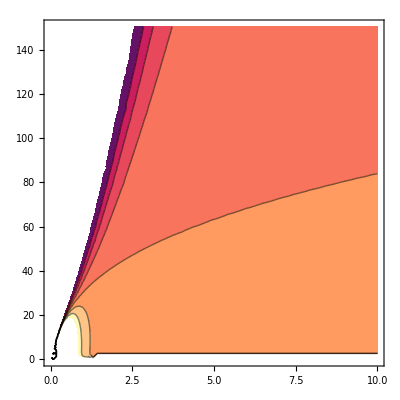

```mathematica
Vreal=AH3/(s^2 τ^3)+(AF0 τ^3)/s^4+(AF2 τ)/s^4+AF4/(s^4 τ^1)+AD6/s^3+AD5/(s^3 τ^(1/2))+(AD7 τ^(1/2))/s^3;
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
max=20;
data=Table[0,{i,1,max}];
Do[
{min,steps}=Reap[
NMinimize[
{10^3 diV⟦1⟧^2+10^3 diV⟦2⟧^2+10^5(Abs[Vreal]-Vreal)+10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij),s>10taur,τ>10 taur},{s,τ,AF0,AF2,AF4,AH3,AD5,AD6,AD7},
Method->{"SimulatedAnnealing","PerturbationScale"->0.5,"LevelIterations"->50,"RandomSeed"->0,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^3,WorkingPrecision->10^3,AccuracyGoal->20}},
StepMonitor:>Sow[{s,τ,AF0,AF2,AF4,AH3,AD5,AD6,AD7}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,1]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,10},{τ,0,150.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
$MaxExtraPrecision=10000;
datag=Table[0,{i,max}];
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;10⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[diV/.data⟦jj⟧⟦4;;10⟧/.fr]==0.,
(*Print["--------------------------------------------------------------------------------------------"];*)
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;10⟧,fr,data⟦jj⟧⟦4;;10⟧,egval/.fr/.data⟦jj⟧⟦4;;10⟧}],20];
(*Print["values = ",{Vreal/.fr /.data⟦jj⟧⟦4;;10⟧,egval}/.data⟦jj⟧⟦4;;10⟧/.fr];
Print["diV = ",Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.data⟦jj⟧⟦4;;10⟧/.fr];*)
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
```

1

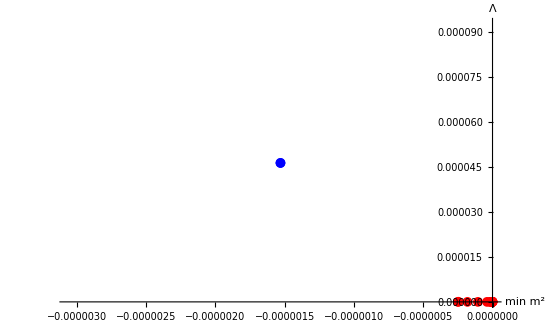

```mathematica
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦11;;12⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦11;;12⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1,f0]
```

```mathematica
datag//TableForm
```

0.000046257 | s→19.143 | τ→21.096 | AF0→0.0005375 | AF2→-1.1242 | AF4→-0.55669 | AH3→-1.609 | AD5→0.73852 | AD6→0.10908 | AD7→0.22525 | -1.5305×10^-6 | 4.6207×10^-7

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

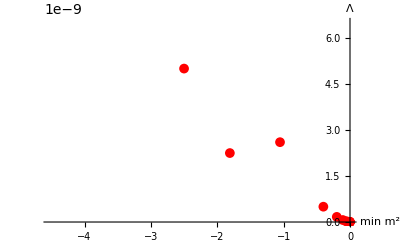
s→-((-3/2 (-57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→(12 2^(1/4) (171-39 √21)^(3/4) (-149423+32607 √21) √(-Graphics-))/((57-13 √21)^4 √-Graphics-) | AD7→(3 ⅈ (-3)^(1/8) √(-316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (-57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→-((-3/2 (-57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→(12 2^(1/4) (171-39 √21)^(3/4) (-149423+32607 √21) √(-Graphics-))/((57-13 √21)^4 √-Graphics-) | AD7→-(3 ⅈ (-3)^(1/8) √(-316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (-57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→(ⅈ (-3/2 (-57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→(12 ⅈ 2^(1/4) (171-39 √21)^(3/4) (-149423+32607 √21) √(-Graphics-))/((57-13 √21)^4 √-Graphics-) | AD7→-(3 (-1)^(3/8) 3^(1/8) √(-316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (-57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→(ⅈ (-3/2 (-57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→(12 ⅈ 2^(1/4) (171-39 √21)^(3/4) (-149423+32607 √21) √(-Graphics-))/((57-13 √21)^4 √-Graphics-) | AD7→(3 (-1)^(3/8) 3^(1/8) √(-316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (-57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→-(ⅈ (-3/2 (-57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→-(12 ⅈ 2^(1/4) (171-39 √21)^(3/4) (-149423+32607 √21) √(-Graphics-))/((57-13 √21)^4 √-Graphics-) | AD7→-(3 (-1)^(7/8) 3^(1/8) √(-316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (-57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→-(ⅈ (-3/2 (-57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→-(12 ⅈ 2^(1/4) (171-39 √21)^(3/4) (-149423+32607 √21) √(-Graphics-))/((57-13 √21)^4 √-Graphics-) | AD7→(3 (-1)^(7/8) 3^(1/8) √(-316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (-57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→((-3/2 (-57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→-(12 2^(1/4) (171-39 √21)^(3/4) (-149423+32607 √21) √(-Graphics-))/((57-13 √21)^4 √-Graphics-) | AD7→-(3 (-3)^(1/8) √(-316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (-57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→((-3/2 (-57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→-(12 2^(1/4) (171-39 √21)^(3/4) (-149423+32607 √21) √(-Graphics-))/((57-13 √21)^4 √-Graphics-) | AD7→(3 (-3)^(1/8) √(-316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (-57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→-((3/2 (57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→-(12 2^(1/4) (171+39 √21)^(3/4) (149423+32607 √21) √(-Graphics-))/((57+13 √21)^4 √-Graphics-) | AD7→-(3 ⅈ 3^(1/8) √(316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→-((3/2 (57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→-(12 2^(1/4) (171+39 √21)^(3/4) (149423+32607 √21) √(-Graphics-))/((57+13 √21)^4 √-Graphics-) | AD7→(3 ⅈ 3^(1/8) √(316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→((3/2 (57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→(12 2^(1/4) (171+39 √21)^(3/4) (149423+32607 √21) √(-Graphics-))/((57+13 √21)^4 √-Graphics-) | AD7→-(3 3^(1/8) √(316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→((3/2 (57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→(12 2^(1/4) (171+39 √21)^(3/4) (149423+32607 √21) √(-Graphics-))/((57+13 √21)^4 √-Graphics-) | AD7→(3 3^(1/8) √(316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→(ⅈ (3/2 (57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→-(12 ⅈ 2^(1/4) (171+39 √21)^(3/4) (149423+32607 √21) √(-Graphics-))/((57+13 √21)^4 √-Graphics-) | AD7→-(3 (-1)^(1/4) 3^(1/8) √(316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→(ⅈ (3/2 (57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→-(12 ⅈ 2^(1/4) (171+39 √21)^(3/4) (149423+32607 √21) √(-Graphics-))/((57+13 √21)^4 √-Graphics-) | AD7→(3 (-1)^(1/4) 3^(1/8) √(316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→-(ⅈ (3/2 (57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→(12 ⅈ 2^(1/4) (171+39 √21)^(3/4) (149423+32607 √21) √(-Graphics-))/((57+13 √21)^4 √-Graphics-) | AD7→(3 (-1)^(3/4) 3^(1/8) √(316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (57+13 √21)^(11/8) (-Graphics-)^(1/4))
s→-(ⅈ (3/2 (57+13 √21))^(1/4) (-Graphics-)^(3/2))/(h √-Graphics-) | t→(12 ⅈ 2^(1/4) (171+39 √21)^(3/4) (149423+32607 √21) √(-Graphics-))/((57+13 √21)^4 √-Graphics-) | AD7→-(3 (-1)^(3/4) 3^(1/8) √(316+69 √21) h -Graphics-^(5/4))/(2^(5/8) (57+13 √21)^(11/8) (-Graphics-)^(1/4))

{{-(2 (2/3)^(1/4) h^6 -Graphics-^(7/2))/((57+13 √21)^(5/4) (-Graphics-)^(15/2))+((57+13 √21)^11 h^6 -Graphics-^(7/2))/(3456 2^(3/4) (171+39 √21)^(9/4) (149423+32607 √21)^3 (-Graphics-)^(15/2))+(5 (57+13 √21)^(5/2) h^6 -Graphics-^(7/2))/(24 √3 (2 (171+39 √21))^(3/4) (149423+32607 √21) (-Graphics-)^(15/2))+(480 2^(1/4) √3 (171+39 √21)^(9/4) (149423+32607 √21)^3 h^6 -Graphics-^(7/2))/((57+13 √21)^(27/2) (-Graphics-)^(15/2))+(24 2^(3/4) (3 (171+39 √21))^(3/8) √((316+69 √21) (149423+32607 √21)) h^6 √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(15/4))/((57+13 √21)^(37/8) (-Graphics-)^(31/4)),-(2 (2/3)^(1/4) h^6 -Graphics-^(7/2))/((57+13 √21)^(5/4) (-Graphics-)^(15/2))+((57+13 √21)^11 h^6 -Graphics-^(7/2))/(3456 2^(3/4) (171+39 √21)^(9/4) (149423+32607 √21)^3 (-Graphics-)^(15/2))+(5 (57+13 √21)^(5/2) h^6 -Graphics-^(7/2))/(24 √3 (2 (171+39 √21))^(3/4) (149423+32607 √21) (-Graphics-)^(15/2))+(480 2^(1/4) √3 (171+39 √21)^(9/4) (149423+32607 √21)^3 h^6 -Graphics-^(7/2))/((57+13 √21)^(27/2) (-Graphics-)^(15/2))+(24 2^(3/4) (3 (171+39 √21))^(3/8) √((316+69 √21) (149423+32607 √21)) h^6 √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(15/4))/((57+13 √21)^(37/8) (-Graphics-)^(31/4))},{-(((57+13 √21)^(31/8) √(316+69 √21) h^4 -Graphics-^(11/4))/(96 2^(1/4) 3^(1/8) (171+39 √21)^(9/8) (149423+32607 √21)^(3/2) (-Graphics-)^(19/4) ((√(-Graphics-))/(√-Graphics-))^(3/2)))+((57+13 √21)^20 h^4 -Graphics-^(7/2))/(165888 2^(3/4) √(3 (57+13 √21)) (171+39 √21)^(15/4) (149423+32607 √21)^5 (-Graphics-)^(11/2))+((57+13 √21)^11 h^4 -Graphics-^(7/2))/(13824 2^(3/4) (171+39 √21)^(9/4) (149423+32607 √21)^3 (-Graphics-)^(11/2))+(3 (1/2 (171+39 √21))^(3/4) (149423+32607 √21) h^4 -Graphics-^(7/2))/((57+13 √21)^5 (-Graphics-)^(11/2)),-(((57+13 √21)^(31/8) √(316+69 √21) h^4 -Graphics-^(11/4))/(96 2^(1/4) 3^(1/8) (171+39 √21)^(9/8) (149423+32607 √21)^(3/2) (-Graphics-)^(19/4) ((√(-Graphics-))/(√-Graphics-))^(3/2)))+((57+13 √21)^20 h^4 -Graphics-^(7/2))/(165888 2^(3/4) √(3 (57+13 √21)) (171+39 √21)^(15/4) (149423+32607 √21)^5 (-Graphics-)^(11/2))+((57+13 √21)^11 h^4 -Graphics-^(7/2))/(13824 2^(3/4) (171+39 √21)^(9/4) (149423+32607 √21)^3 (-Graphics-)^(11/2))+(3 (1/2 (171+39 √21))^(3/4) (149423+32607 √21) h^4 -Graphics-^(7/2))/((57+13 √21)^5 (-Graphics-)^(11/2))}}

{(h^4 (4340338538328212474521190196522509334198553411096113149578057875456 √(2 (149423+32607 √21) (94465211+20613999 √21)) h^2 -Graphics-+947139518743953480822780677211627402032225098935477303471142600704 √(42 (149423+32607 √21) (94465211+20613999 √21)) h^2 -Graphics--102451446207931340705162501381144699468182009387622290573855579441201152 √(2 (316+69 √21)) (-Graphics-)^3-22356738443121039188316883549173130524640944711130480750249348398317568 √(42 (316+69 √21)) (-Graphics-)^3-√((-4340338538328212474521190196522509334198553411096113149578057875456 √(2 (149423+32607 √21) (94465211+20613999 √21)) h^2 -Graphics--947139518743953480822780677211627402032225098935477303471142600704 √(42 (149423+32607 √21) (94465211+20613999 √21)) h^2 -Graphics-+102451446207931340705162501381144699468182009387622290573855579441201152 √(2 (316+69 √21)) (-Graphics-)^3+22356738443121039188316883549173130524640944711130480750249348398317568 √(42 (316+69 √21)) (-Graphics-)^3+75484956528567467079230952066843959855480688259771987541595016365342720 √(149423+32607 √21) h^2 (-Graphics-)^(3/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)+16472167958219592029618729376843805804470326670119391875153170771476480 √(21 (149423+32607 √21)) h^2 (-Graphics-)^(3/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)-289853761929170726496082415967219837426310766146680047399081393258496000 √(149423+32607 √21) (-Graphics-)^(11/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)-63251276405149244882343708367389238713397767351035454629235407192064000 √(21 (149423+32607 √21)) (-Graphics-)^(11/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4))^2-4 (-6602078359133572115944816905360037500864000000000000000000000000000000000000000000000000000000000 √(2 (94465211+20613999 √21)) h^2 (-Graphics-)^(15/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)+22091799832203132080890499939664384000000000000000000000000000000000000000000000000000000000 (149423+32607 √21) √(2 (94465211+20613999 √21)) h^2 (-Graphics-)^(15/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)-1440691610688711757422226975409668138176000000000000000000000000000000000000000000000000000000000 √(42 (94465211+20613999 √21)) h^2 (-Graphics-)^(15/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)+4820839452828976995915156594881856000000000000000000000000000000000000000000000000000000000 (149423+32607 √21) √(42 (94465211+20613999 √21)) h^2 (-Graphics-)^(15/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)))-75484956528567467079230952066843959855480688259771987541595016365342720 √(149423+32607 √21) h^2 (-Graphics-)^(3/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)-16472167958219592029618729376843805804470326670119391875153170771476480 √(21 (149423+32607 √21)) h^2 (-Graphics-)^(3/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)+289853761929170726496082415967219837426310766146680047399081393258496000 √(149423+32607 √21) (-Graphics-)^(11/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)+63251276405149244882343708367389238713397767351035454629235407192064000 √(21 (149423+32607 √21)) (-Graphics-)^(11/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)) -Graphics-^(11/4))/(26873856 2^(3/4) 3^(1/4) (57+13 √21)^(65/4) (149423+32607 √21)^(13/2) (-Graphics-)^(31/4) ((√(-Graphics-))/(√-Graphics-))^(3/2)),(h^4 (4340338538328212474521190196522509334198553411096113149578057875456 √(2 (149423+32607 √21) (94465211+20613999 √21)) h^2 -Graphics-+947139518743953480822780677211627402032225098935477303471142600704 √(42 (149423+32607 √21) (94465211+20613999 √21)) h^2 -Graphics--102451446207931340705162501381144699468182009387622290573855579441201152 √(2 (316+69 √21)) (-Graphics-)^3-22356738443121039188316883549173130524640944711130480750249348398317568 √(42 (316+69 √21)) (-Graphics-)^3+√((-4340338538328212474521190196522509334198553411096113149578057875456 √(2 (149423+32607 √21) (94465211+20613999 √21)) h^2 -Graphics--947139518743953480822780677211627402032225098935477303471142600704 √(42 (149423+32607 √21) (94465211+20613999 √21)) h^2 -Graphics-+102451446207931340705162501381144699468182009387622290573855579441201152 √(2 (316+69 √21)) (-Graphics-)^3+22356738443121039188316883549173130524640944711130480750249348398317568 √(42 (316+69 √21)) (-Graphics-)^3+75484956528567467079230952066843959855480688259771987541595016365342720 √(149423+32607 √21) h^2 (-Graphics-)^(3/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)+16472167958219592029618729376843805804470326670119391875153170771476480 √(21 (149423+32607 √21)) h^2 (-Graphics-)^(3/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)-289853761929170726496082415967219837426310766146680047399081393258496000 √(149423+32607 √21) (-Graphics-)^(11/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)-63251276405149244882343708367389238713397767351035454629235407192064000 √(21 (149423+32607 √21)) (-Graphics-)^(11/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4))^2-4 (-6602078359133572115944816905360037500864000000000000000000000000000000000000000000000000000000000 √(2 (94465211+20613999 √21)) h^2 (-Graphics-)^(15/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)+22091799832203132080890499939664384000000000000000000000000000000000000000000000000000000000 (149423+32607 √21) √(2 (94465211+20613999 √21)) h^2 (-Graphics-)^(15/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)-1440691610688711757422226975409668138176000000000000000000000000000000000000000000000000000000000 √(42 (94465211+20613999 √21)) h^2 (-Graphics-)^(15/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)+4820839452828976995915156594881856000000000000000000000000000000000000000000000000000000000 (149423+32607 √21) √(42 (94465211+20613999 √21)) h^2 (-Graphics-)^(15/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)))-75484956528567467079230952066843959855480688259771987541595016365342720 √(149423+32607 √21) h^2 (-Graphics-)^(3/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)-16472167958219592029618729376843805804470326670119391875153170771476480 √(21 (149423+32607 √21)) h^2 (-Graphics-)^(3/4) √((√(-Graphics-))/(√-Graphics-)) -Graphics-^(1/4)+289853761929170726496082415967219837426310766146680047399081393258496000 √(149423+32607 √21) (-Graphics-)^(11/4) √((√(-Graphics-))/(√(-Graphics-))) (-Graphics-)^(1/4)+63251276405149244882343708367389238713397767351035454629235407192064000 √(21 (149423+32607 √21)) (-Graphics-)^(11/4) √((√(-Graphics-))/(√(-Graphics-))) (-Graphics-)^(1/4)) (-Graphics-)^(11/4))/(26873856 2^(3/4) 3^(1/4) (57+13 √21)^(65/4) (149423+32607 √21)^(13/2) (-Graphics-)^(31/4) ((√(-Graphics-))/(√(-Graphics-)))^(3/2))}

```mathematica
VF=h^2/(8 s^2 t^3)+(f0^2 t^3)/(32 s^4)+(3 f4^2)/(32 s^4 t)- (f0 h)/(4 s^3)+(AD7 t^(1/2))/s^3;
sol=PowerExpand@Simplify@Solve[{VF==0,D[VF,s]==0,D[VF,t]==0},{s,t,AD7}];
TableForm[sol]
var={s,t};
Table[D[VF,var⟦i⟧,var⟦i⟧],{i,2},{j,2}]/.sol⟦12⟧
Eigenvalues[%]
```

```mathematica
detmij-trmij^2/4
```

-(16 AF2^2)/s^10+(256 AF0 AF4)/s^10+(36 AH3^2)/(s^6 τ^8)+(204 AF4 AH3)/(s^8 τ^6)+(261 AD5 AH3)/(2 s^7 τ^(11/2))+(144 AD6 AH3)/(s^7 τ^5)+(321 AD7 AH3)/(2 s^7 τ^(9/2))+(24 AF4^2)/(s^10 τ^4)+(288 AF2 AH3)/(s^8 τ^4)+(27 AD5 AF4)/(s^9 τ^(7/2))+(24 AD6 AF4)/(s^9 τ^3)+(27 AD5^2)/(4 s^8 τ^3)+(31 AD7 AF4)/(s^9 τ^(5/2))+(9 AD5 AD6)/(s^8 τ^(5/2))+(72 AF2 AF4)/(s^10 τ^2)+(21 AD5 AD7)/(2 s^8 τ^2)+(420 AF0 AH3)/(s^8 τ^2)+(27 AD5 AF2)/(s^9 τ^(3/2))-(3 AD6 AD7)/(s^8 τ^(3/2))-(21 AD7^2)/(4 s^8 τ)-(17 AD7 AF2)/(s^9 √τ)+(123 AD5 AF0 √τ)/s^9+(72 AD6 AF0 τ)/s^9+(31 AD7 AF0 τ^(3/2))/s^9+(24 AF0 AF2 τ^2)/s^10-(24 AF0^2 τ^4)/s^10-1/4 ((48 AH3 s^2+8 AF4 τ^2+3 AD5 s τ^(5/2)-AD7 s τ^(7/2)+24 AF0 τ^6)/(4 s^4 τ^5)+(6 AH3 s^2+4 τ^2 (5 AF4+3 AD5 s √τ+3 AD6 s τ+3 AD7 s τ^(3/2)+5 AF2 τ^2+5 AF0 τ^4))/(s^6 τ^3))^2

```mathematica
Sin[π/6]
```

1/2

## Caso Non-geometric

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VO3=AO3 PowerExpand[(ρ^((3-6)/2)τ^-3)/.changmoduli]/.{ϕ->Log[1/s]};
VF5=AF5 PowerExpand[(ρ^(3-p)τ^-4)/.changmoduli]/.{ϕ->Log[1/s]}/.{p->5};
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
VNG=ANG/(s τ);
Vreal=VH3+VF3+VF5+VO3+VNG
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
max=1000;
data=Table[0,{i,1,max}];
Do[
{min,steps}=Reap[
NMinimize[
{10^4 diV.diV+10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij)+0 10^3(Abs[AD5]-AD5),s>RandomInteger[{1,100}]/100,τ>RandomInteger[{1,100}]/100},{s,τ,AF3,AH3,AO3,ANG,AF5},
Method->{"SimulatedAnnealing","PerturbationScale"->0.5,"LevelIterations"->50,"RandomSeed"->0,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^2,WorkingPrecision->10^3}},
StepMonitor:>Sow[{s,τ,AF3,AH3,AO3,ANG,AF5}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,100]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,2},{τ,0,10},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

AF5/τ^4+AO3/τ^3+AF3/(s τ^3)+(AH3 s)/τ^3+ANG/(s τ)

_______________________________________________________ taur = 100

min = {0.004415070522,{s→1.356791756,τ→3.123272294,AF3→0.446895074,AH3→0.3508582231,AO3→-0.1710463198,ANG→0.01930519819,AF5→-1.54706111}}

diV = {0.0001903364446,-0.0006366153391}

m^2 = {-0.00701492232,0.01692433675}

_______________________________________________________ taur = 200

min = {6.17979777×10^-10,{s→1.139845344,τ→2.38351084,AF3→-0.3288716392,AH3→0.5440592467,AO3→-0.3989885569,ANG→0.182311839,AF5→-0.4210262836}}

diV = {1.736478212×10^-7,1.778887627×10^-7}

m^2 = {-0.05262813076,0.09031745381}

_______________________________________________________ taur = 300

min = {0.005266086896,{s→0.8076395559,τ→3.644624892,AF3→-0.6330507319,AH3→0.04294439545,AO3→-0.007519611821,ANG→0.05025549761,AF5→1.203315844}}

diV = {-0.000205702411,0.0006959132185}

m^2 = {-0.0108909387,0.01231622287}

_______________________________________________________ taur = 400

min = {0.004442313581,{s→1.298866922,τ→3.056254527,AF3→0.5832072313,AH3→0.6383039091,AO3→-1.94537776,ANG→0.05408902475,AF5→1.190922885}}

diV = {-0.000240486971,0.0006216086992}

m^2 = {0.0008210684245,0.03609249741}

_______________________________________________________ taur = 500

min = {0.009054441641,{s→5.6444425,τ→4.14509246,AF3→-1.551019255,AH3→-0.08151078365,AO3→1.045053935,ANG→0.0001516045962,AF5→-0.7103127199}}

diV = {-0.0004620856867,-0.000831817878}

m^2 = {-0.0004122394764,0.0004122394764}

_______________________________________________________ taur = 600

min = {2.379873029×10^-7,{s→1.607038543,τ→1.801028245,AF3→-0.9045693377,AH3→0.05697799966,AO3→-0.1587656724,ANG→0.3242304539,AF5→0.5564050756}}

diV = {7.929426341×10^-7,4.813519738×10^-6}

m^2 = {-0.07368901418,0.0819564295}

_______________________________________________________ taur = 700

min = {0.003455728924,{s→0.9292834377,τ→3.281342289,AF3→0.07978162585,AH3→0.9272032662,AO3→-0.268235549,ANG→0.06657165934,AF5→-2.249994299}}

diV = {0.0001353732818,-0.0005720550384}

m^2 = {-0.01355860884,0.05918038234}

_______________________________________________________ taur = 800

min = {0.0003990589569,{s→2.076746001,τ→3.850352526,AF3→-0.6781712658,AH3→0.8843908616,AO3→-2.552475431,ANG→0.3054017992,AF5→0.8820266444}}

diV = {-0.0001430188183,0.0001394686822}

m^2 = {-0.008068935647,0.01891277755}

_______________________________________________________ taur = 900

min = {0.0001299228949,{s→2.027948078,τ→1.582861483,AF3→-1.455543053,AH3→0.2729356135,AO3→-1.156586366,ANG→1.02969374,AF5→1.064653577}}

diV = {-0.0001125640825,-0.00001793367824}

m^2 = {-0.160048358,0.2427889513}

_______________________________________________________ taur = 1000

min = {0.00009981585065,{s→1.305831872,τ→2.650802527,AF3→-0.0591423218,AH3→0.1695585901,AO3→-0.03157660892,ANG→0.04920147305,AF5→-0.4608783719}}

diV = {0.00008017310173,-0.00005961425018}

m^2 = {-0.01194516954,0.01649533393}

-Graphics-

```mathematica
vars={s,τ,AF3,AH3,AO3,ANG,AF5};(*|1|*)
ListLogPlot[Table[(10^4 diV.diV+ 10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+ 10^5(Abs[trmij]-trmij)+0 10^3(Abs[AD5]-AD5))/.Thread[vars->steps⟦1⟧⟦jj⟧],{jj,1,100}]]
```

-Graphics-

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
(*data=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];*)
$MaxExtraPrecision=10000;
max=Length[data];
datag=Table[0,{i,max}]; 
up=Length[data⟦1⟧]-2;
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;up⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[Re[diV/.data⟦jj⟧⟦4;;up⟧/.fr]]==0.0,
(*Print["--------------------------------------------------------------------------------------------"];*)
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;up⟧,fr,data⟦jj⟧⟦4;;up⟧,egval/.fr/.data⟦jj⟧⟦4;;up⟧}],30];
(*Print["values = ",{Vreal/.fr /.data⟦jj⟧⟦4;;8⟧,egval}/.data⟦jj⟧⟦4;;8⟧/.fr];
Print["diV = ",Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.data⟦jj⟧⟦4;;8⟧/.fr];*)
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦up+1;;up+2⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦up+1;;up+2⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1]
{ListPlot[Table[{τ/.datag⟦i⟧⟦3⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re τ","Λ"},PlotStyle-> Blue],ListPlot[Table[{s/.datag⟦i⟧⟦2⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re s","Λ"},PlotStyle-> Blue]}
(*Save["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty",datag];*)
```

976

-Graphics-

{-Graphics-,-Graphics-}

```mathematica
(*datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];*)
```

```mathematica
Print["Stable dS"];
up=Length[datag⟦1⟧]-2;
aux1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Length[aux1]
Grid[aux1, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
Print["Stable AdS"];
aux2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Length[aux2]
Grid[aux2, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

Stable dS

59

20 | 0.00068221 | 0.029149 | 0.18727 | {s→0.72407,τ→2.1962,AF3→0.063283,AH3→0.66044,AO3→-1.7091,ANG→0.058669,AF5→1.669}
21 | 0.0062509 | 0.010998 | 0.12423 | {s→1.4609,τ→1.6208,AF3→-0.10647,AH3→0.11284,AO3→-0.69867,ANG→0.13219,AF5→0.6412}
24 | 0.0013606 | 0.00086365 | 0.0079204 | {s→1.9299,τ→2.9591,AF3→-0.14054,AH3→0.095825,AO3→-0.74436,ANG→0.05681,AF5→1.2125}
64 | 0.0019981 | 0.00022787 | 0.0059584 | {s→1.8481,τ→3.2518,AF3→-0.13798,AH3→0.11654,AO3→-0.73599,ANG→0.05069,AF5→1.216}
67 | 0.0017954 | 0.00054915 | 0.0076884 | {s→1.7503,τ→3.0687,AF3→-0.13868,AH3→0.11235,AO3→-0.73749,ANG→0.051276,AF5→1.2155}
158 | 0.0013357 | 0.00095497 | 0.0087368 | {s→1.8281,τ→2.9235,AF3→-0.14013,AH3→0.098935,AO3→-0.74327,ANG→0.055082,AF5→1.213}
162 | 0.00028721 | 0.0008255 | 0.0050349 | {s→3.1458,τ→2.9132,AF3→1.7839,AH3→0.19436,AO3→-1.2831,ANG→0.016441,AF5→0.19637}
164 | 0.00027569 | 0.00033423 | 0.0019298 | {s→2.7902,τ→3.9419,AF3→-0.12811,AH3→0.074681,AO3→-0.85779,ANG→0.045662,AF5→1.8051}
175 | 0.00004541 | 0.00046996 | 0.0024816 | {s→2.5157,τ→3.784,AF3→-0.128,AH3→0.076071,AO3→-0.8574,ANG→0.042561,AF5→1.8055}
191 | 0.0014589 | 0.00075421 | 0.0073166 | {s→1.9714,τ→3.0041,AF3→-0.14028,AH3→0.09638,AO3→-0.7441,ANG→0.057047,AF5→1.2126}
207 | 0.001306 | 0.0009468 | 0.0084938 | {s→1.8742,τ→2.9272,AF3→-0.14053,AH3→0.096725,AO3→-0.74407,ANG→0.056054,AF5→1.2126}
219 | 0.0061841 | 0.0033274 | 0.021706 | {s→2.4025,τ→2.1346,AF3→0.18874,AH3→0.12647,AO3→-0.81759,ANG→0.11877,AF5→0.57652}
261 | 0.0017961 | 0.00049802 | 0.0069712 | {s→1.8442,τ→3.1034,AF3→-0.13917,AH3→0.10886,AO3→-0.73925,ANG→0.052892,AF5→1.2147}
266 | 0.00014784 | 0.00049699 | 0.0017846 | {s→2.5306,τ→4.2482,AF3→0.11039,AH3→0.12071,AO3→-1.0893,ANG→0.036716,AF5→2.0802}
276 | 0.0041248 | 0.00022789 | 0.009252 | {s→2.7254,τ→2.9589,AF3→-0.35054,AH3→0.11682,AO3→-1.1033,ANG→0.13915,AF5→1.6967}
280 | 0.00011545 | 0.00051759 | 0.0018169 | {s→2.5315,τ→4.2236,AF3→0.11032,AH3→0.11965,AO3→-1.0896,ANG→0.036797,AF5→2.0801}
293 | 0.000036145 | 0.00056923 | 0.0019072 | {s→2.505,τ→4.1738,AF3→0.11019,AH3→0.1186,AO3→-1.0899,ANG→0.036398,AF5→2.08}
298 | 0.0013928 | 0.00089056 | 0.0083736 | {s→1.8497,τ→2.9472,AF3→-0.13996,AH3→0.099265,AO3→-0.74315,ANG→0.055212,AF5→1.2131}
317 | 0.000010744 | 0.00058125 | 0.0019202 | {s→2.5345,τ→4.1514,AF3→0.11012,AH3→0.11644,AO3→-1.0904,ANG→0.03701,AF5→2.0799}
347 | 0.013198 | 0.00049159 | 0.041972 | {s→1.8991,τ→1.9565,AF3→0.33987,AH3→0.22543,AO3→-0.9591,ANG→0.1236,AF5→0.3947}
360 | 0.000039411 | 0.00056458 | 0.0018933 | {s→2.5328,τ→4.1699,AF3→0.11013,AH3→0.11733,AO3→-1.0903,ANG→0.036951,AF5→2.0799}
391 | 0.000039282 | 0.00056272 | 0.0018864 | {s→2.5503,τ→4.1664,AF3→0.11012,AH3→0.11647,AO3→-1.0904,ANG→0.037296,AF5→2.0798}
395 | 0.0038094 | 0.0040906 | 0.047875 | {s→1.257,τ→2.804,AF3→0.58321,AH3→0.6383,AO3→-1.9454,ANG→0.054089,AF5→1.1909}
407 | 0.0013366 | 0.0009643 | 0.0088419 | {s→1.8143,τ→2.9199,AF3→-0.14002,AH3→0.099465,AO3→-0.74309,ANG→0.054825,AF5→1.2131}
415 | 0.000343 | 0.00032425 | 0.0019107 | {s→2.6983,τ→3.9751,AF3→-0.12787,AH3→0.078582,AO3→-0.85675,ANG→0.0443,AF5→1.8056}
431 | 0.0018751 | 0.00037104 | 0.0062061 | {s→1.9057,τ→3.1758,AF3→-0.13904,AH3→0.10934,AO3→-0.73918,ANG→0.053158,AF5→1.2147}
468 | 0.0019717 | 0.0024113 | 0.021529 | {s→1.1648,τ→3.0717,AF3→-0.010218,AH3→0.30963,AO3→-1.2316,ANG→0.045606,AF5→1.743}
471 | 0.028483 | 0.051914 | 0.22966 | {s→2.0136,τ→1.2409,AF3→0.43262,AH3→0.20357,AO3→-0.99223,ANG→0.25506,AF5→0.28149}
520 | 0.0055947 | 0.0033938 | 0.024526 | {s→1.8097,τ→2.5864,AF3→0.084269,AH3→0.256,AO3→-1.3728,ANG→0.11274,AF5→1.4046}
568 | 0.00046705 | 0.002771 | 0.011287 | {s→1.5211,τ→2.349,AF3→0.16133,AH3→0.10465,AO3→-0.40044,ANG→0.014649,AF5→0.20698}
578 | 0.0012875 | 0.00099407 | 0.0088893 | {s→1.8299,τ→2.9098,AF3→-0.14038,AH3→0.097965,AO3→-0.74362,ANG→0.055324,AF5→1.2128}
599 | 0.0014159 | 0.00082431 | 0.0078057 | {s→1.9186,τ→2.9742,AF3→-0.14025,AH3→0.097287,AO3→-0.74382,ANG→0.056338,AF5→1.2128}
602 | 0.001724 | 0.00055927 | 0.0070138 | {s→1.8796,τ→3.0793,AF3→-0.13961,AH3→0.10554,AO3→-0.74068,ANG→0.054048,AF5→1.2141}
603 | 0.0014329 | 0.00075903 | 0.0072308 | {s→2.0001,τ→3.0028,AF3→-0.14049,AH3→0.09491,AO3→-0.74462,ANG→0.05769,AF5→1.2124}
608 | 0.00016051 | 0.0004865 | 0.0017551 | {s→2.5708,τ→4.249,AF3→0.11037,AH3→0.1191,AO3→-1.0896,ANG→0.037486,AF5→2.0801}
614 | 0.00013495 | 0.00050378 | 0.0017884 | {s→2.5529,τ→4.2334,AF3→0.11034,AH3→0.11918,AO3→-1.0896,ANG→0.037184,AF5→2.0801}
623 | 0.0046356 | 0.00090732 | 0.012909 | {s→2.989,τ→2.8573,AF3→-0.30845,AH3→0.14147,AO3→-1.4652,ANG→0.19259,AF5→2.0792}
633 | 0.0013202 | 0.00094355 | 0.0085328 | {s→1.8622,τ→2.9282,AF3→-0.14041,AH3→0.097411,AO3→-0.74381,ANG→0.055772,AF5→1.2127}
638 | 0.000011072 | 0.00058361 | 0.0019287 | {s→2.5151,τ→4.1549,AF3→0.11009,AH3→0.11739,AO3→-1.0903,ANG→0.036638,AF5→2.0799}
640 | 0.00002598 | 0.00057544 | 0.0019171 | {s→2.5074,τ→4.1662,AF3→0.11013,AH3→0.11819,AO3→-1.0901,ANG→0.036469,AF5→2.08}
660 | 0.00090119 | 0.0010699 | 0.0033072 | {s→3.1169,τ→2.8644,AF3→0.75798,AH3→0.10671,AO3→-0.75928,ANG→0.033964,AF5→0.3302}
682 | 0.000030088 | 0.00048822 | 0.0025574 | {s→2.4672,τ→3.7699,AF3→-0.12804,AH3→0.077003,AO3→-0.85728,ANG→0.041991,AF5→1.8055}
713 | 0.0033933 | 0.0067007 | 0.099927 | {s→0.84896,τ→1.9508,AF3→-0.11404,AH3→0.17843,AO3→-0.77383,ANG→0.063762,AF5→0.96769}
730 | 0.0035516 | 0.00075783 | 0.025685 | {s→2.0641,τ→1.81,AF3→-0.079199,AH3→0.034461,AO3→-0.27702,ANG→0.068991,AF5→0.28204}
742 | 0.000039282 | 0.00056272 | 0.0018864 | {s→2.5503,τ→4.1664,AF3→0.11012,AH3→0.11647,AO3→-1.0904,ANG→0.037296,AF5→2.0798}
750 | 0.0067935 | 0.0052838 | 0.03251 | {s→2.1069,τ→2.1876,AF3→0.98073,AH3→0.32238,AO3→-1.5014,ANG→0.094091,AF5→0.46831}
775 | 0.000025495 | 0.00033762 | 0.001664 | {s→1.7187,τ→4.3769,AF3→-0.010684,AH3→0.098257,AO3→-0.67937,ANG→0.015708,AF5→1.5046}
807 | 0.0019653 | 0.00024921 | 0.0057569 | {s→1.9063,τ→3.2481,AF3→-0.13851,AH3→0.11301,AO3→-0.73768,ANG→0.052055,AF5→1.2153}
809 | 0.0014042 | 0.00080622 | 0.0075596 | {s→1.9626,τ→2.9825,AF3→-0.14048,AH3→0.095571,AO3→-0.74442,ANG→0.057178,AF5→1.2125}
830 | 0.0012823 | 0.0017365 | 0.014529 | {s→2.2421,τ→2.0523,AF3→-0.023066,AH3→0.038558,AO3→-0.32204,ANG→0.051495,AF5→0.32883}
859 | 0.0018751 | 0.00037104 | 0.0062061 | {s→1.9057,τ→3.1758,AF3→-0.13904,AH3→0.10934,AO3→-0.73918,ANG→0.053158,AF5→1.2147}
871 | 0.00028721 | 0.0008255 | 0.0050349 | {s→3.1458,τ→2.9132,AF3→1.7839,AH3→0.19436,AO3→-1.2831,ANG→0.016441,AF5→0.19637}
891 | 0.0011848 | 0.0011112 | 0.0095925 | {s→1.7867,τ→2.8701,AF3→-0.14059,AH3→0.097726,AO3→-0.74374,ANG→0.054936,AF5→1.2128}
899 | 0.0015066 | 0.00024876 | 0.034968 | {s→1.1794,τ→2.1579,AF3→-0.14852,AH3→0.071729,AO3→-0.52969,ANG→0.05332,AF5→0.8106}
940 | 0.00017472 | 0.00047785 | 0.0017432 | {s→2.5644,τ→4.2616,AF3→0.11041,AH3→0.11987,AO3→-1.0894,ANG→0.037327,AF5→2.0802}
946 | 2.3993×10^-6 | 0.00056888 | 0.0018864 | {s→2.6654,τ→4.1209,AF3→0.10987,AH3→0.11022,AO3→-1.092,ANG→0.039639,AF5→2.0793}
948 | 0.0027847 | 0.0022258 | 0.012256 | {s→1.9272,τ→2.8071,AF3→0.22033,AH3→0.20005,AO3→-1.0671,ANG→0.066332,AF5→1.0039}
969 | 0.0018522 | 0.00039525 | 0.0062562 | {s→1.9137,τ→3.1637,AF3→-0.13918,AH3→0.10827,AO3→-0.73963,ANG→0.05352,AF5→1.2145}
975 | 0.016728 | 0.030893 | 0.19123 | {s→1.5512,τ→1.6559,AF3→0.027275,AH3→0.2945,AO3→-1.4884,ANG→0.2485,AF5→1.0774}

Stable AdS

40

40 | -0.000017851 | 0.00059965 | 0.001954 | {s→2.5282,τ→4.1333,AF3→0.10994,AH3→0.11596,AO3→-1.0908,ANG→0.03695,AF5→2.0797}
66 | -0.000047941 | 0.00060259 | 0.0019521 | {s→2.6229,τ→4.0975,AF3→0.10976,AH3→0.1108,AO3→-1.092,ANG→0.038865,AF5→2.0792}
106 | -0.00006749 | 0.00061548 | 0.0019773 | {s→2.6098,τ→4.0879,AF3→0.10969,AH3→0.1109,AO3→-1.0921,ANG→0.038635,AF5→2.0792}
177 | -0.000050179 | 0.00060544 | 0.0019577 | {s→2.6135,τ→4.0977,AF3→0.10975,AH3→0.11117,AO3→-1.0919,ANG→0.038684,AF5→2.0792}
192 | -0.000019534 | 0.0005993 | 0.0019518 | {s→2.5385,τ→4.1302,AF3→0.10992,AH3→0.11542,AO3→-1.0909,ANG→0.037159,AF5→2.0796}
195 | -0.000038166 | 0.00060004 | 0.0019474 | {s→2.6061,τ→4.1062,AF3→0.1098,AH3→0.1118,AO3→-1.0917,ANG→0.038522,AF5→2.0793}
262 | -0.000040948 | 0.00060126 | 0.0019497 | {s→2.6081,τ→4.1042,AF3→0.10978,AH3→0.11164,AO3→-1.0918,ANG→0.038566,AF5→2.0793}
268 | -0.000028755 | 0.00059523 | 0.0019382 | {s→2.6031,τ→4.1126,AF3→0.10984,AH3→0.11217,AO3→-1.0916,ANG→0.038448,AF5→2.0794}
284 | -0.00005019 | 0.00061376 | 0.0019756 | {s→2.5629,τ→4.1062,AF3→0.10975,AH3→0.11347,AO3→-1.0915,ANG→0.037695,AF5→2.0794}
301 | -0.000028159 | 0.00059685 | 0.001942 | {s→2.5905,τ→4.1151,AF3→0.10984,AH3→0.11276,AO3→-1.0915,ANG→0.0382,AF5→2.0794}
310 | -0.000069121 | 0.00062091 | 0.001988 | {s→2.584,τ→4.0912,AF3→0.10967,AH3→0.11202,AO3→-1.0919,ANG→0.038134,AF5→2.0792}
311 | -0.000036306 | 0.00059741 | 0.001942 | {s→2.6158,τ→4.1057,AF3→0.10981,AH3→0.11141,AO3→-1.0918,ANG→0.038709,AF5→2.0793}
344 | -0.000079168 | 0.00062303 | 0.001992 | {s→2.6028,τ→4.0822,AF3→0.10965,AH3→0.11092,AO3→-1.0921,ANG→0.038514,AF5→2.0791}
362 | -0.000026345 | 0.00060432 | 0.0019618 | {s→2.5319,τ→4.1269,AF3→0.10988,AH3→0.11555,AO3→-1.0909,ANG→0.037044,AF5→2.0796}
384 | -0.000038993 | 0.00059857 | 0.0019442 | {s→2.6178,τ→4.1038,AF3→0.1098,AH3→0.11125,AO3→-1.0919,ANG→0.038751,AF5→2.0793}
403 | -0.000053562 | 0.00060701 | 0.0019608 | {s→2.615,τ→4.0954,AF3→0.10974,AH3→0.11101,AO3→-1.092,ANG→0.038719,AF5→2.0792}
458 | -0.000038993 | 0.00059857 | 0.0019442 | {s→2.6178,τ→4.1038,AF3→0.1098,AH3→0.11125,AO3→-1.0919,ANG→0.038751,AF5→2.0793}
490 | -0.000060071 | 0.00062028 | 0.001988 | {s→2.5573,τ→4.1012,AF3→0.10971,AH3→0.11348,AO3→-1.0915,ANG→0.037599,AF5→2.0794}
501 | -0.000036099 | 0.00060562 | 0.0019605 | {s→2.5631,τ→4.1149,AF3→0.10981,AH3→0.11383,AO3→-1.0913,ANG→0.037676,AF5→2.0795}
518 | -0.000029578 | 0.00060018 | 0.0019495 | {s→2.574,τ→4.1171,AF3→0.10984,AH3→0.11348,AO3→-1.0914,ANG→0.03788,AF5→2.0795}
524 | -0.00007286 | 0.00062367 | 0.0019933 | {s→2.5799,τ→4.0896,AF3→0.10966,AH3→0.11211,AO3→-1.0919,ANG→0.03806,AF5→2.0792}
544 | -0.000046951 | 0.00060396 | 0.0019548 | {s→2.6118,τ→4.0999,AF3→0.10976,AH3→0.11132,AO3→-1.0919,ANG→0.038647,AF5→2.0793}
553 | -0.000061296 | 0.00061713 | 0.0019809 | {s→2.5807,τ→4.0964,AF3→0.1097,AH3→0.11237,AO3→-1.0918,ANG→0.038059,AF5→2.0793}
554 | -5.8226×10^-6 | 0.00058987 | 0.0019335 | {s→2.5453,τ→4.1383,AF3→0.11003,AH3→0.11546,AO3→-1.0907,ANG→0.037253,AF5→2.0797}
677 | -9.645×10^-6 | 0.00059118 | 0.0019348 | {s→2.5527,τ→4.1344,AF3→0.11001,AH3→0.11501,AO3→-1.0909,ANG→0.037408,AF5→2.0797}
715 | -0.000016728 | 0.00059762 | 0.0019488 | {s→2.5382,τ→4.1321,AF3→0.10994,AH3→0.11551,AO3→-1.0909,ANG→0.037146,AF5→2.0797}
729 | -0.000047526 | 0.00061068 | 0.0019692 | {s→2.5727,τ→4.1061,AF3→0.10976,AH3→0.11308,AO3→-1.0916,ANG→0.037884,AF5→2.0794}
732 | -0.000069121 | 0.00062091 | 0.001988 | {s→2.584,τ→4.0912,AF3→0.10967,AH3→0.11202,AO3→-1.0919,ANG→0.038134,AF5→2.0792}
740 | -0.000047256 | 0.00061148 | 0.0019711 | {s→2.5667,τ→4.1073,AF3→0.10976,AH3→0.11337,AO3→-1.0915,ANG→0.037765,AF5→2.0794}
768 | -1.4161×10^-6 | 0.00050067 | 0.0026083 | {s→2.4614,τ→3.7543,AF3→-0.12813,AH3→0.076489,AO3→-0.8575,ANG→0.041969,AF5→1.8054}
778 | -0.000025 | 0.00060027 | 0.0019515 | {s→2.5551,τ→4.1235,AF3→0.10987,AH3→0.11449,AO3→-1.0911,ANG→0.037498,AF5→2.0796}
780 | -0.000024662 | 0.0005937 | 0.0019356 | {s→2.598,τ→4.1161,AF3→0.10986,AH3→0.11251,AO3→-1.0915,ANG→0.038339,AF5→2.0794}
787 | -0.000073734 | 0.00062222 | 0.0019904 | {s→2.5909,τ→4.0873,AF3→0.10966,AH3→0.11159,AO3→-1.092,ANG→0.038276,AF5→2.0792}
788 | -0.000027647 | 0.00059851 | 0.0019461 | {s→2.5777,τ→4.1177,AF3→0.10985,AH3→0.11337,AO3→-1.0914,ANG→0.037948,AF5→2.0795}
806 | -0.00004179 | 0.00060717 | 0.0019625 | {s→2.5743,τ→4.1094,AF3→0.10978,AH3→0.11316,AO3→-1.0915,ANG→0.037905,AF5→2.0794}
826 | -0.0010778 | 0.00017835 | 0.00097969 | {s→1.5234,τ→6.0037,AF3→0.63052,AH3→0.15439,AO3→-1.0459,ANG→-0.0075525,AF5→2.055}
832 | -0.000038993 | 0.00059857 | 0.0019442 | {s→2.6178,τ→4.1038,AF3→0.1098,AH3→0.11125,AO3→-1.0919,ANG→0.038751,AF5→2.0793}
846 | -0.000021343 | 0.00059899 | 0.0019499 | {s→2.5487,τ→4.1271,AF3→0.1099,AH3→0.11489,AO3→-1.091,ANG→0.037363,AF5→2.0796}
862 | -0.000053519 | 0.00061531 | 0.0019783 | {s→2.565,τ→4.1038,AF3→0.10973,AH3→0.11328,AO3→-1.0916,ANG→0.037742,AF5→2.0794}
912 | -0.0004484 | 0.0010537 | 0.0026037 | {s→1.7186,τ→3.463,AF3→0.12138,AH3→0.083314,AO3→-0.50595,ANG→0.010397,AF5→0.69595}

```mathematica
Histogram[Flatten@Table[data⟦jj⟧⟦9;;10⟧,{jj,Length[data]}]]
```

-Graphics-

```mathematica
up=Length[datag⟦1⟧]-2;
datag1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
datag2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{datag1⟦jj⟧⟦1⟧,AO3/.datag1⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag1]}];
l2=Table[{datag2⟦jj⟧⟦1⟧,AO3/.datag2⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag2]}];
f1=ListPlot[{l1,l2},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20},AxesLabel->{"Λ","A_O3"},ImageSize->700]
```

-Graphics-

```mathematica
inter=101;
Print["values = ",datag⟦inter⟧];
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧]
{Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"}],
Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"τ","V"}]}
Plot3D[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1}]
```

values = {0.022335,s→2.1161,τ→2.8103,AF3→-0.8214,AH3→0.29409,AO3→-1.2827,ANG→0.27075,AF5→1.5,-0.0098342,0.023007}

diV = {0.,0.}

{-Graphics-,-Graphics-}

-Graphics3D-

```mathematica
(*Save["C:\\Users\\Cesar\\Dropbox\\Source-codes\\penalty-cases-AdS-noT",data]*)
```

```mathematica
caseso3=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g"];
f1=ListPlot[Table[{Min[caseso3⟦i⟧⟦9;;10⟧],caseso3⟦i⟧⟦1⟧},{i,Length[caseso3]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o7g"];
f2=ListPlot[Table[{Min[caseso3g⟦i⟧⟦9;;10⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g"];
f3=ListPlot[Table[{Min[caseso3g⟦i⟧⟦8;;9⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Green,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g-pos"];
f4=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦8;;9⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];
f5=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦10;;11⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3F5=Get["/Users/cesar/Dropbox/Source-codes/penalty-F5-o3g-noD5-2"];
f6=ListPlot[Table[{Min[caseso3F5⟦i⟧⟦8;;9⟧],caseso3F5⟦i⟧⟦1⟧},{i,Length[caseso3F5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];
casenoAR=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
f7=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
casenoARnp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty"];
f8=ListPlot[Table[{Min[casenoARnp⟦i⟧⟦9;;10⟧],casenoARnp⟦i⟧⟦1⟧},{i,Length[casenoARnp]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
Show[f5,f6,f1,f3,f2]
Show[f8,f7]
```

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o7g.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o5g.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o5g-pos.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-F5-o3g-noD5-2.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6.

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty.

-Graphics-

-Graphics-

```mathematica
datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];
up=Length[datag⟦1⟧]-2;
varsNN={AF3,AH3,AD5,AR6,AO3,AF5};
dataNNv=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->Chop[datag⟦jj⟧⟦1⟧],{jj,1,Length[datag]}];
dataNNs=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->(Chop[s/.datag⟦jj⟧⟦2;;up⟧]),{jj,1,Length[datag]}];
dataNNτ=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->(Chop[τ/.datag⟦jj⟧⟦2;;up⟧]),{jj,1,Length[datag]}];
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->"Scalar"];
trainedv=NetTrain[net,dataNNv,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{45,Tanh,1},"Input"->6,"Output"->"Scalar"];
traineds=NetTrain[net,dataNNs,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->"Scalar"];
trainedτ=NetTrain[net,dataNNτ,Method->{"ADAM","L2Regularization"->0.005}]
(*net=NetChain[{32,Tanh,1},"Input"->6,"Output"->1]
net1=NetTrain[net,dataNN,BatchSize->1024]*)
```

Get::noopen: Cannot open /Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

NetDecoder::deprec: "NetDecoder[{Scalar,…}]" setting has been deprecated. Use ""Real" or "Integer" bare port specifications" setting instead.

NetTrain::nodata: No training data provided.

$Failed

NetDecoder::deprec: "NetDecoder[{Scalar,…}]" setting has been deprecated. Use ""Real" or "Integer" bare port specifications" setting instead.

NetTrain::nodata: No training data provided.

$Failed

NetDecoder::deprec: "NetDecoder[{Scalar,…}]" setting has been deprecated. Use ""Real" or "Integer" bare port specifications" setting instead.

NetTrain::nodata: No training data provided.

$Failed